## Equations

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

SetOptions[ContractMetric,AllowUpperDerivatives->True];
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l}]

(*DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},FlatMetric->True,PrintAs->"g"];*)
DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},FlatMetric->False,PrintAs->"g"];

SetOptions[ContractMetric,AllowUpperDerivatives->True];

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensor[PhiC[],M4,PrintAs->"φ^*"]

DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[d][Phi[]]CD[-d][PhiC[]]]]
```

(∇_d φ^* ∇^d φ)

```mathematica
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[α]
```

```mathematica
DefTensor[n[a],M4]
DefTensor[nc[a],M4]
DefTensor[n2[a,b],M4]
DefTensor[nc2[a,b],M4]

Rulescalartovector=MakeRule[{CD[b][Phi[]],n[b]}]
Rulescalartovector2=MakeRule[{CD[b][PhiC[]],nc[b]}]

Rulevectosca=MakeRule[{n[b],CD[b][Phi[]]}]
Rulevectosca2=MakeRule[{nc[b],CD[b][PhiC[]]}]

Rule3=MakeRule[{CD[a][n[b]],n2[a,b]}]
Rule3inv=MakeRule[{n2[a,b],CD[a][n[b]]}]

Rule4=MakeRule[{CD[a][nc[b]],nc2[a,b]}]
Rule4inv=MakeRule[{nc2[a,b],CD[a][nc[b]]}]

(*ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};*)
(*rule:={Rulevectosca,Rulevectosca2,Rule3inv, Rule4inv, ruleflat}*)
rule:={Rulevectosca,Rulevectosca2,Rule3inv, Rule4inv}
```

{HoldPattern[∇^UnderBar[b̲] φ]:>Module[{},n | b
 ]}

{HoldPattern[∇^UnderBar[b̲] φ^*]:>Module[{},nc | b
 ]}

{HoldPattern[n | UnderBar[b̲]
 ]:>Module[{},∇^b φ]}

{HoldPattern[nc | UnderBar[b̲]
 ]:>Module[{},∇^b φ^*]}

{HoldPattern[∇^UnderBar[a̲] n | UnderBar[b̲]
 ]:>Module[{},n2 | a | b
  |  ]}

{HoldPattern[n2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a n | b
 ]}

{HoldPattern[∇^UnderBar[a̲] nc | UnderBar[b̲]
 ]:>Module[{},nc2 | a | b
  |  ]}

{HoldPattern[nc2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a nc | b
 ]}

### Test

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
Ltry=Sqrt[-Detmetric[]]( -X[]-mS^2 Phi[]PhiC[]+ka*RicciScalarCD[])//NoScalar
LtryC=(Ltry//NoScalar)/.Rulescalartovector/.Rulescalartovector2
```

√(-g^OverTilde[~]) (-m^2 φ φ^*+k R[∇]-∇_a φ^* ∇^a φ)

√(-g^OverTilde[~]) (-n | a
  nc |  
a-m^2 φ φ^*+k R[∇])

j^μ=dL/(d(d_μ ϕ))δϕ

```mathematica
cj=VarD[n[i]][LtryC]deltaPhi+VarD[nc[i]][LtryC]deltaPhiC/.Rulevectosca/.Rulevectosca2/.ruleflat//ContractMetric//Simplification
```

-ⅈ α (φ^* ∇_i φ-φ ∇_i φ^*)

### Test Cisterna

```mathematica
DefConstantSymbol[ka, PrintAs ->"k"];
```

```mathematica
LH=Sqrt[-Detmetric[]]*(ka*RicciScalarCD[]-(X[]-EinsteinCD[a,b]CD[-a][Phi[]]CD[-b][PhiC[]]));
LHC=(LH//NoScalar)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4
```

√(-g^OverTilde[~]) (G[∇] | a | b
  |   n |  
a nc |  
b-n | c
  nc |  
c+k R[∇])

```mathematica
(*current*)
```

j^μ=dL/(d(d_μ ϕ))δϕ+d_ν(dL/(d(d_μ d_ν ϕ))δϕ)-2d_ν(dL/(d(d_μ d_ν ϕ)))δϕ

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
cj1H=VarD[n[a]][LHC]deltaPhi+VarD[nc[a]][LHC]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2H=CD[b][(VarD[n2[a, b]][LHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LHC]deltaPhiC)]//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3H=-2CD[b][VarD[n2[a, b]][LHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LHC]]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jHDown=cj1H+cj2H+cj3H//Simplification//ContractMetric//Simplification;
jH2Down=Collect[(ContractMetric[SortCovDs[jHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{α ,eta},Simplify]
```

-ⅈ α √(-g^OverTilde[~]) (φ^* ∇_a φ-φ ∇_a φ^*+G[∇] |   |  
a | b (-φ^* ∇^b φ+φ ∇^b φ^*))

```mathematica
ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};
```

```mathematica
Simplify[%]/.ruleflat
```

1/2 ⅈ α (∇_a φ^* (2 φ+2 η ∇_b ∇^b φ)-∇_a φ (2 φ^*+2 η ∇_b ∇^b φ^*)+2 η (∇_b ∇_a φ^* ∇^b φ-∇_b ∇_a φ ∇^b φ^*))

```mathematica
Collect[%,{α ,eta},Simplify]
```

α (-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)+ⅈ η (∇_a φ^* ∇_b ∇^b φ-∇_a φ ∇_b ∇^b φ^*+∇_b ∇_a φ^* ∇^b φ-∇_b ∇_a φ ∇^b φ^*))

### Paper

```mathematica
DefConstantSymbol[Mp, PrintAs ->"Mp"];
DefConstantSymbol[L3, PrintAs ->"Λ"];
DefConstantSymbol[c4, PrintAs ->"c"];
DefConstantSymbol[d4, PrintAs ->"d"];
```

```mathematica
LP=1/2 Mp^2 RicciScalarCD[]-X[]-mS^2*PhiC[]*Phi[]+Mp/L3^3(c4 X[] RicciScalarCD[]-2 c4 (CD[-h]@CD[h]@Phi[]*CD[-f]@CD[f]@PhiC[]-CD[f]@CD[h]@Phi[]*CD[-f]@CD[-h]@PhiC[])+d4*1/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][PhiC[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][PhiC[]]]));
LHC=((LP//NoScalar)//ContractMetric)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4
```

-n | a
  nc |  
a-(2 c Mp n2 |   | h
h |   nc2 |   | f
f |)/Λ^3+(2 c Mp n2 | f | h
  |   nc2 |   |  
f | h)/Λ^3-m^2 φ φ^*+(Mp^2 R[∇])/2+(c Mp n | a
  nc |  
a R[∇])/Λ^3-(d Mp n |  
a n2 |   | c
b |   nc | b
  nc2 |   | a
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | b
b |   nc | c
  nc2 |   | a
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | c
b |   nc | a
  nc2 |   | b
c |)/(Λ^3 (n | a
  nc |  
a))-(d Mp n |  
a n2 |   | a
b |   nc | c
  nc2 |   | b
c |)/(Λ^3 (n | a
  nc |  
a))-(d Mp n |  
a n2 |   | b
b |   nc | a
  nc2 |   | c
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | a
b |   nc | b
  nc2 |   | c
c |)/(Λ^3 (n | a
  nc |  
a))

```mathematica
(*current*)
```

j^μ=dL/(d(d_μ ϕ))δϕ+d_ν(dL/(d(d_μ d_ν ϕ))δϕ)-2d_ν(dL/(d(d_μ d_ν ϕ)))δϕ

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
cj1H=VarD[n[a]][LHC]deltaPhi+VarD[nc[a]][LHC]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2H=CD[b][(VarD[n2[a, b]][LHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LHC]deltaPhiC)]//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3H=-2CD[b][VarD[n2[a, b]][LHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LHC]]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jHDown=cj1H+cj2H+cj3H//Simplification//ContractMetric//Simplification;
jH2Down=Collect[(ContractMetric[SortCovDs[jHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{α ,c4,d4},Simplify]
```

α (-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)+(ⅈ c Mp (-∇_a φ^* (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (φ^* R[∇]+2 ∇_b ∇^b φ^*)-2 φ^* R[∇] |   |  
a | b ∇^b φ-2 ∇_b ∇_a φ^* ∇^b φ+2 φ R[∇] |   |  
a | b ∇^b φ^*+2 ∇_b ∇_a φ ∇^b φ^*))/Λ^3+1/(Λ^3 (∇_a φ^* ∇^a φ)^2)ⅈ d Mp ((∇_a φ^* ∇^a φ) (2 φ^* ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ+∇_b ∇_a φ^* (φ^* ∇^b φ-2 φ ∇^b φ^*) ∇_c ∇^c φ-φ^* ∇_a φ ∇_b ∇^b φ ∇_c ∇^c φ^*+∇_a φ ∇_b φ^* ∇^b φ ∇_c ∇^c φ^*+φ^* ∇_b ∇_a φ ∇^b φ ∇_c ∇^c φ^*-2 φ ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ^*-φ^* R[∇] |   |  
a | c ∇_b φ^* ∇^b φ ∇^c φ-∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ+φ R[∇] |   |  
a | c ∇_b φ^* ∇^b φ ∇^c φ^*+∇_b φ ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*-∇_a φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*-2 φ^* ∇^b φ^* ∇_c ∇_b φ ∇^c ∇_a φ-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c ∇_a φ+2 φ ∇^b φ^* ∇_c ∇_b φ^* ∇^c ∇_a φ-φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c ∇_b φ+2 φ ∇^b φ^* ∇_c ∇_a φ^* ∇^c ∇_b φ+φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c ∇^b φ+∇_a φ^* (-∇_b φ ∇^b φ ∇_c ∇^c φ^*+∇_b ∇^b φ (-φ^* ∇_c ∇^c φ+2 φ ∇_c ∇^c φ^*)+φ^* R[∇] |   |  
b | c ∇^b φ ∇^c φ+∇^b φ ∇_c ∇_b φ^* ∇^c φ-φ R[∇] |   |  
b | c ∇^b φ ∇^c φ^*+φ^* ∇_c ∇_b φ ∇^c ∇^b φ-2 φ ∇_c ∇_b φ^* ∇^c ∇^b φ)+φ^* R[∇] |   |   |   |  
a | b | c | d ∇^b φ ∇^c φ ∇^d φ^*)+∇^b φ (-φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c φ^* ∇_d ∇^d φ-φ^* ∇_a φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ^*-φ^* ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*+φ^* ∇_a φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+∇_a φ^* (φ^* ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ+∇_c ∇_b φ^* (φ ∇^c φ^* ∇_d ∇^d φ+∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))-φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ-φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*)+φ^* ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+∇_b φ^* (φ^* ∇_a φ ∇_c ∇^c φ ∇_d ∇^d φ^*-φ ∇_a φ^* ∇_c ∇^c φ ∇_d ∇^d φ^*+∇_c ∇_a φ^* ∇^c φ (-φ^* ∇_d ∇^d φ+φ ∇_d ∇^d φ^*)+∇_c ∇_a φ ∇^c φ^* (-φ^* ∇_d ∇^d φ+φ ∇_d ∇^d φ^*)+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*-φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ-φ^* ∇_a φ ∇_d ∇_c φ^* ∇^d ∇^c φ+φ ∇_a φ^* ∇_d ∇_c φ^* ∇^d ∇^c φ))))

```mathematica
(*Simplificando*)
```

```mathematica
term1=-ⅈ (SuperStar[φ] ∇_a φ-φ ∇_a SuperStar[φ])
```

-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)

```mathematica
term2=(ⅈ c Mp (-∇_a SuperStar[φ] (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (SuperStar[φ] R[∇]+2 ∇_b ∇^b SuperStar[φ])-2 SuperStar[φ] {{R[∇], {{, }, {a, b}}}} ∇^b φ-2 ∇_b ∇_a SuperStar[φ] ∇^b φ+2 φ {{R[∇], {{, }, {a, b}}}} ∇^b SuperStar[φ]+2 ∇_b ∇_a φ ∇^b SuperStar[φ]))/Λ^3;
Simplification[Numerator[term2]]
```

ⅈ c Mp (-∇_a φ^* (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (φ^* R[∇]+2 ∇_b ∇^b φ^*)-2 φ^* R[∇] |   |  
a | b ∇^b φ-2 ∇_b ∇_a φ^* ∇^b φ+2 φ R[∇] |   |  
a | b ∇^b φ^*+2 ∇_b ∇_a φ ∇^b φ^*)

```mathematica
term3=1/(Λ^3 (∇_a SuperStar[φ] ∇^a φ)^2)ⅈ d Mp ((∇_a SuperStar[φ] ∇^a φ) (2 SuperStar[φ] ∇_b ∇_a φ ∇^b SuperStar[φ] ∇_c ∇^c φ+∇_b ∇_a SuperStar[φ] (SuperStar[φ] ∇^b φ-2 φ ∇^b SuperStar[φ]) ∇_c ∇^c φ-SuperStar[φ] ∇_a φ ∇_b ∇^b φ ∇_c ∇^c SuperStar[φ]+∇_a φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇^c SuperStar[φ]+SuperStar[φ] ∇_b ∇_a φ ∇^b φ ∇_c ∇^c SuperStar[φ]-2 φ ∇_b ∇_a φ ∇^b SuperStar[φ] ∇_c ∇^c SuperStar[φ]-SuperStar[φ] {{R[∇], {{, }, {a, c}}}} ∇_b SuperStar[φ] ∇^b φ ∇^c φ-∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ+φ {{R[∇], {{, }, {a, c}}}} ∇_b SuperStar[φ] ∇^b φ ∇^c SuperStar[φ]+∇_b φ ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-∇_a φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]-2 SuperStar[φ] ∇^b SuperStar[φ] ∇_c ∇_b φ ∇^c ∇_a φ-SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c ∇_a φ+2 φ ∇^b SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c ∇_a φ-SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c ∇_b φ+2 φ ∇^b SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c ∇_b φ+SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c ∇^b φ+∇_a SuperStar[φ] (-∇_b φ ∇^b φ ∇_c ∇^c SuperStar[φ]+∇_b ∇^b φ (-SuperStar[φ] ∇_c ∇^c φ+2 φ ∇_c ∇^c SuperStar[φ])+SuperStar[φ] {{R[∇], {{, }, {b, c}}}} ∇^b φ ∇^c φ+∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ-φ {{R[∇], {{, }, {b, c}}}} ∇^b φ ∇^c SuperStar[φ]+SuperStar[φ] ∇_c ∇_b φ ∇^c ∇^b φ-2 φ ∇_c ∇_b SuperStar[φ] ∇^c ∇^b φ)+SuperStar[φ] {{R[∇], {{, , , }, {a, b, c, d}}}} ∇^b φ ∇^c φ ∇^d SuperStar[φ])+∇^b φ (-SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇^d φ-SuperStar[φ] ∇_a φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇^d SuperStar[φ]-SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_b ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+∇_a SuperStar[φ] (SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇^d φ+∇_c ∇_b SuperStar[φ] (φ ∇^c SuperStar[φ] ∇_d ∇^d φ+∇^c φ (SuperStar[φ] ∇_d ∇^d φ-φ ∇_d ∇^d SuperStar[φ]))-SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ-SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ])+SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+∇_b SuperStar[φ] (SuperStar[φ] ∇_a φ ∇_c ∇^c φ ∇_d ∇^d SuperStar[φ]-φ ∇_a SuperStar[φ] ∇_c ∇^c φ ∇_d ∇^d SuperStar[φ]+∇_c ∇_a SuperStar[φ] ∇^c φ (-SuperStar[φ] ∇_d ∇^d φ+φ ∇_d ∇^d SuperStar[φ])+∇_c ∇_a φ ∇^c SuperStar[φ] (-SuperStar[φ] ∇_d ∇^d φ+φ ∇_d ∇^d SuperStar[φ])+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-SuperStar[φ] ∇_a φ ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ+φ ∇_a SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ)))//NoScalar;
tem=Simplification[Numerator[term3]]
```

-ⅈ d Mp ∇^b φ (φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c φ^* ∇_d ∇^d φ+φ^* ∇_a φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ^*+φ^* ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*-∇_b φ ∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*-φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*-φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*-φ^* ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*+φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*+φ ∇_b ∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇_a φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ^* ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+∇_a φ^* (-φ^* ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ+∇_b φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*-∇_c ∇_b φ^* (φ ∇^c φ^* ∇_d ∇^d φ+∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ+φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*+∇_b φ^* (∇_c ∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*)-∇^c φ ∇_d ∇_c φ^* ∇^d φ+R[∇] |   |  
c | d ∇^c φ (-φ^* ∇^d φ+φ ∇^d φ^*)-φ^* ∇_d ∇_c φ ∇^d ∇^c φ+φ ∇_d ∇_c φ^* ∇^d ∇^c φ))+∇_b φ^* (-∇_a φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*+φ ∇_c ∇_a φ^* (2 ∇^c φ^* ∇_d ∇^d φ-∇^c φ ∇_d ∇^d φ^*)-∇_c ∇_a φ (φ^* ∇^c φ ∇_d ∇^d φ^*+∇^c φ^* (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))+φ^* R[∇] |   |  
a | d ∇_c φ^* ∇^c φ ∇^d φ+∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ-φ R[∇] |   |  
a | d ∇_c φ^* ∇^c φ ∇^d φ^*+∇_a φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ-2 φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ+φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*+φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ-φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ-φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*))

```mathematica
-ⅈ d Mp ∇^b φ (SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ] Bϕ+SuperStar[φ] ∇_a φ ∇_c ∇_b φ ∇^c SuperStar[φ]BϕC+SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]-∇_b φ ∇_c SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]+φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]+φ ∇_b ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+∇_a SuperStar[φ] (-SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ] Bϕ+∇_b φ ∇_c SuperStar[φ] ∇^c φ BϕC-∇_c ∇_b SuperStar[φ] (φ ∇^c SuperStar[φ] Bϕ+∇^c φ (SuperStar[φ]Bϕ-φ BϕC))+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ+SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ]+∇_b SuperStar[φ] (BϕC (SuperStar[φ]BϕC-φ BϕC)-∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d φ+{{R[∇], {{, }, {c, d}}}} ∇^c φ (-SuperStar[φ] ∇^d φ+φ ∇^d SuperStar[φ])-SuperStar[φ] ∇_d ∇_c φ ∇^d ∇^c φ+φ ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ))+∇_b SuperStar[φ] (-∇_a φ ∇_c SuperStar[φ] ∇^c φ  BϕC+φ ∇_c ∇_a SuperStar[φ] (2 ∇^c SuperStar[φ]Bϕ-∇^c φ  BϕC)-∇_c ∇_a φ (SuperStar[φ] ∇^c φ  BϕC+∇^c SuperStar[φ] (SuperStar[φ]Bϕ-φ  BϕC))+SuperStar[φ] {{R[∇], {{, }, {a, d}}}} XX∇^d φ+XX ∇_d ∇_a SuperStar[φ] ∇^d φ-φ {{R[∇], {{, }, {a, d}}}} XX ∇^d SuperStar[φ]+∇_a φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ-2 φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ+φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]+SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} ∇^c φ ∇^d φ ∇^e SuperStar[φ]))//Expand
```

```mathematica
ⅈ BϕC^2 d Mp φ ∇_a SuperStar[φ] XX-ⅈ BϕC^2 d Mp SuperStar[φ] ∇_a SuperStar[φ] XX-ⅈ BϕC d Mp ∇_a SuperStar[φ] ∇_b φ ∇^b φ ∇_c SuperStar[φ] ∇^c φ+ⅈ BϕC d Mp ∇_a φ XX XX+ⅈ BϕC d Mp SuperStar[φ] XX ∇_c ∇_a φ ∇^c φ+ⅈ BϕC d Mp φ XX ∇_c ∇_a SuperStar[φ] ∇^c φ-ⅈ BϕC d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ+ⅈ Bϕ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ-ⅈ BϕC d Mp φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ]+ⅈ Bϕ d Mp SuperStar[φ] XX ∇_c ∇_a φ ∇^c SuperStar[φ]-2 ⅈ Bϕ d Mp φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-ⅈ BϕC d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ]+ⅈ Bϕ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ]-ⅈ Bϕ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]+ⅈ Bϕ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]-ⅈ d Mp XX SuperStar[φ] {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d φ+ⅈ d Mp SuperStar[φ] {{R[∇], {{, }, {c, d}}}} ∇_a SuperStar[φ] XX ∇^c φ ∇^d φ-ⅈ d Mp XX ∇_b SuperStar[φ] ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d φ+ⅈ d Mp ∇_a SuperStar[φ] XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d φ+ⅈ d Mp XX φ {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d SuperStar[φ]-ⅈ d Mp φ {{R[∇], {{, }, {c, d}}}} ∇_a SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇^d SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+ⅈ d Mp ∇_b φ ∇^b φ XX ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-ⅈ d Mp φ ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp ∇_a φ XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp φ ∇_b ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp SuperStar[φ] XX ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+2 ⅈ d Mp φ XX ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-ⅈ d Mp φ XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ-ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+ⅈ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-ⅈ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+ⅈ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp φ XX ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] XX ∇_d ∇_c φ ∇^d ∇^c φ-ⅈ d Mp φ ∇_a SuperStar[φ] XX ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ+ⅈ d Mp SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} XX ∇^c φ ∇^d φ ∇^e SuperStar[φ]//FullSimplify
```

ⅈ d Mp (BϕC XX φ^* ∇_c ∇_a φ ∇^c φ+BϕC XX φ ∇_c ∇_a φ^* ∇^c φ+Bϕ XX φ^* ∇_c ∇_a φ ∇^c φ^*-BϕC φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*-2 Bϕ φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*-XX φ^* R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ-XX ∇_b φ^* ∇^b φ ∇_d ∇_a φ^* ∇^d φ+XX φ R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ^*-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+XX ∇_b φ ∇^b φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇^b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-XX φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+2 XX φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ-XX φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*-φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ+XX φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+∇_a φ (XX (BϕC XX-∇^c φ ∇_d ∇_c φ^* ∇^d φ^*)+φ^* ∇^b φ ∇^c φ^* (-BϕC ∇_c ∇_b φ-Bϕ ∇_c ∇_b φ^*+∇_d ∇_c φ^* ∇^d ∇_b φ+∇_d ∇_b φ^* ∇^d ∇_c φ))+∇_a φ^* (-BϕC ∇_b φ ∇^b φ ∇_c φ^* ∇^c φ-∇^b φ (-Bϕ φ^* ∇_c ∇_b φ ∇^c φ^*+∇_c ∇_b φ^* ((BϕC φ-Bϕ φ^*) ∇^c φ-Bϕ φ ∇^c φ^*)+φ R[∇] |   |  
c | d ∇_b φ^* ∇^c φ ∇^d φ^*+(φ^* ∇^c φ^* ∇_d ∇_c φ+(φ^* ∇^c φ+φ ∇^c φ^*) ∇_d ∇_c φ^*) ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*)+XX (BϕC^2 (φ-φ^*)+φ^* R[∇] |   |  
c | d ∇^c φ ∇^d φ+φ^* ∇_d ∇_c φ ∇^d ∇^c φ+∇_d ∇_c φ^* (∇^c φ ∇^d φ-φ ∇^d ∇^c φ)))+XX φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*)

```mathematica
Collect[(BϕC XX SuperStar[φ] ∇_c ∇_a φ ∇^c φ+BϕC XX φ ∇_c ∇_a SuperStar[φ] ∇^c φ+Bϕ XX SuperStar[φ] ∇_c ∇_a φ ∇^c SuperStar[φ]-BϕC φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ]-2 Bϕ φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-XX SuperStar[φ] {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d φ-XX ∇_b SuperStar[φ] ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d φ+XX φ {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d SuperStar[φ]-SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+XX ∇_b φ ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-φ ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_b ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-XX SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+2 XX φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-XX φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+XX φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+∇_a φ (XX (BϕC XX-∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ])+SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] (-BϕC ∇_c ∇_b φ-Bϕ ∇_c ∇_b SuperStar[φ]+∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ))+∇_a SuperStar[φ] (-BϕC ∇_b φ ∇^b φ ∇_c SuperStar[φ] ∇^c φ-∇^b φ (-Bϕ SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ]+∇_c ∇_b SuperStar[φ] ((BϕC φ-Bϕ SuperStar[φ]) ∇^c φ-Bϕ φ ∇^c SuperStar[φ])+φ {{R[∇], {{, }, {c, d}}}} ∇_b SuperStar[φ] ∇^c φ ∇^d SuperStar[φ]+(SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ+(SuperStar[φ] ∇^c φ+φ ∇^c SuperStar[φ]) ∇_d ∇_c SuperStar[φ]) ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ])+XX (BϕC^2 (φ-SuperStar[φ])+SuperStar[φ] {{R[∇], {{, }, {c, d}}}} ∇^c φ ∇^d φ+SuperStar[φ] ∇_d ∇_c φ ∇^d ∇^c φ+∇_d ∇_c SuperStar[φ] (∇^c φ ∇^d φ-φ ∇^d ∇^c φ)))+XX SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} ∇^c φ ∇^d φ ∇^e SuperStar[φ])//Expand,{BϕC,Bϕ,XX}]
```

BϕC^2 XX (φ ∇_a φ^*-φ^* ∇_a φ^*)+BϕC (XX^2 ∇_a φ-∇_a φ^* ∇_b φ ∇^b φ ∇_c φ^* ∇^c φ-φ ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ+XX (φ^* ∇_c ∇_a φ ∇^c φ+φ ∇_c ∇_a φ^* ∇^c φ)-φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*-φ^* ∇_a φ ∇^b φ ∇_c ∇_b φ ∇^c φ^*)+Bϕ (φ^* ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ+XX φ^* ∇_c ∇_a φ ∇^c φ^*-2 φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*+φ^* ∇_a φ^* ∇^b φ ∇_c ∇_b φ ∇^c φ^*-φ^* ∇_a φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*+φ ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*)-φ R[∇] |   |  
c | d ∇_a φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇^d φ^*-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇^b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇_a φ^* ∇^b φ ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ-φ^* ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ+φ^* ∇_a φ ∇^b φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇_a φ^* ∇^b φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*-φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ+φ^* ∇_a φ ∇^b φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+XX (-φ^* R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ+φ^* R[∇] |   |  
c | d ∇_a φ^* ∇^c φ ∇^d φ-∇_b φ^* ∇^b φ ∇_d ∇_a φ^* ∇^d φ+∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ+φ R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ^*+∇_b φ ∇^b φ ∇_d ∇_a φ^* ∇^d φ^*-∇_a φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+2 φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*+φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+φ^* ∇_a φ^* ∇_d ∇_c φ ∇^d ∇^c φ-φ ∇_a φ^* ∇_d ∇_c φ^* ∇^d ∇^c φ+φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*)

```mathematica
(*ContractMetric[SortCovDs[tem,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplify *)
```

```mathematica
(*Flat Space*)
```

```mathematica
ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};
```

```mathematica
Simplify[%]/.ruleflat
```

```mathematica
Collect[%,{α ,eta},Simplify]
```

### Metric

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
(*MatrixForm[metricarray={{-1,0,0,0},{0,1,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]*)
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
MetricInBasis[metric,-esf,metricarray]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];

ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
```

Computed ∇φ | a
 →∇φ |  
b g | a | b
  |   in 0.01479 Seconds

Computed ∇∇φ |   | b
a |  →∇∇φ |   |  
a | c g | b | c
  |   in 0.076244 Seconds

Computed ∇∇φ | a | b
  |  →∇∇φ |   | b
c |   g | a | c
  |   in 0.079708 Seconds

Computed ∇∇∇φ |   |   | c
a | b |  →∇∇∇φ |   |   |  
a | b | d g | c | d
  |   in 0.944307 Seconds

Computed ∇∇∇φ |   | b | c
a |   |  →∇∇∇φ |   |   | c
a | d |   g | b | d
  |   in 1.12221 Seconds

Computed ∇∇∇φ | a | b | c
  |   |  →∇∇∇φ |   | b | c
d |   |   g | a | d
  |   in 1.20843 Seconds

Computed ∇∇∇φ |   | b |  
a |   | c→∇∇∇φ |   |   |  
a | d | c g | b | d
  |   in 0.972129 Seconds

Computed ∇∇∇φ | a | b |  
  |   | c→∇∇∇φ |   | b |  
d |   | c g | a | d
  |   in 0.821831 Seconds

Computed ∇∇∇φ | a |   |  
  | b | c→∇∇∇φ |   |   |  
d | b | c g | a | d
  |   in 0.594207 Seconds

Computed ∇∇∇φ |   |   | c
a | b |  →∇∇∇φ |   |   |  
a | b | d g | c | d
  |   in 0.703476 Seconds

Computed ∇∇∇φ |   | b | c
a |   |  →∇∇∇φ |   |   | c
a | d |   g | b | d
  |   in 0.764178 Seconds

Computed ∇∇∇φ |   |   | c
a | b |  →∇∇∇φ |   |   |  
a | b | d g | c | d
  |   in 0.605668 Seconds

Computed ∇∇∇φ |   | b |  
a |   | c→∇∇∇φ |   |   |  
a | d | c g | b | d
  |   in 0.552424 Seconds

Computed ∇∇∇φ |   |   | c
a | b |  →∇∇∇φ |   |   |  
a | b | d g | c | d
  |   in 0.523728 Seconds

Computed ∇φ^* | a
 →∇φ^* |  
b g | a | b
  |   in 0.01113 Seconds

Computed ∇∇φ^* |   | b
a |  →∇∇φ^* |   |  
a | c g | b | c
  |   in 0.072211 Seconds

Computed ∇∇φ^* | a | b
  |  →∇∇φ^* |   | b
c |   g | a | c
  |   in 0.073585 Seconds

Computed ∇∇∇φ^* |   |   | c
a | b |  →∇∇∇φ^* |   |   |  
a | b | d g | c | d
  |   in 0.884804 Seconds

Computed ∇∇∇φ^* |   | b | c
a |   |  →∇∇∇φ^* |   |   | c
a | d |   g | b | d
  |   in 1.10759 Seconds

Computed ∇∇∇φ^* | a | b | c
  |   |  →∇∇∇φ^* |   | b | c
d |   |   g | a | d
  |   in 0.96733 Seconds

Computed ∇∇∇φ^* |   | b |  
a |   | c→∇∇∇φ^* |   |   |  
a | d | c g | b | d
  |   in 1.00199 Seconds

Computed ∇∇∇φ^* | a | b |  
  |   | c→∇∇∇φ^* |   | b |  
d |   | c g | a | d
  |   in 0.846528 Seconds

Computed ∇∇∇φ^* | a |   |  
  | b | c→∇∇∇φ^* |   |   |  
d | b | c g | a | d
  |   in 0.701522 Seconds

Computed ∇∇∇φ^* |   |   | c
a | b |  →∇∇∇φ^* |   |   |  
a | b | d g | c | d
  |   in 0.801975 Seconds

Computed ∇∇∇φ^* |   | b | c
a |   |  →∇∇∇φ^* |   |   | c
a | d |   g | b | d
  |   in 0.887597 Seconds

Computed ∇∇∇φ^* |   |   | c
a | b |  →∇∇∇φ^* |   |   |  
a | b | d g | c | d
  |   in 0.494416 Seconds

Computed ∇∇∇φ^* |   | b |  
a |   | c→∇∇∇φ^* |   |   |  
a | d | c g | b | d
  |   in 0.657534 Seconds

Computed ∇∇∇φ^* |   |   | c
a | b |  →∇∇∇φ^* |   |   |  
a | b | d g | c | d
  |   in 0.442268 Seconds

```mathematica
j1=term1//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

term1

```mathematica
j2=term2//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-(4 c Mp w (gg[r]^3 NN[r] ϕ[r]^2+NN[r] r ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2),0,0,0}

```mathematica
org[expr_]:=ToValues@ToValues@ComponentArray@ToValues@TraceBasisDummy@ToBasis[esf]@Implode@expr
evalScalar=Scalar[cont_]:>org@cont;
```

```mathematica
noScalar=Scalar[cont_]:>NoScalar[cont];
```

```mathematica
term3/.evalScalar//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-(8 d Mp w NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 gg[r]^3 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),(8 ⅈ d Mp w^2 ϕ[r]^2 ϕ'[r]^2)/(Λ^3 w^2 gg[r]^2 r ϕ[r]^2-Λ^3 NN[r]^2 r ϕ'[r]^2),0,0}

```mathematica
jH=jH2Down/.evalScalar//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-((2 w α (w^4 gg[r]^7 NN[r] (2 c Mp-Λ^3 r^2) ϕ[r]^6-2 c Mp w^4 gg[r]^4 NN[r] r ϕ[r]^5 gg'[r] (-2 ϕ[r]+r ϕ'[r])+4 c Mp w^2 gg[r]^2 NN[r]^3 r ϕ[r]^3 gg'[r] ϕ'[r]^2 (-2 ϕ[r]+r ϕ'[r])+2 Mp NN[r]^5 r ϕ[r] gg'[r] ϕ'[r]^4 (2 (c+d) ϕ[r]-c r ϕ'[r])+gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (4 c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (2 c Mp-Λ^3 r^2) ϕ'[r]^2+4 c Mp w^2 NN[r] (ϕ[r]^2-r^2 ϕ'[r]^2-r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 w^2 gg[r]^5 ϕ[r]^4 (-c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (-2 c Mp+Λ^3 r^2) ϕ'[r]^2+c Mp w^2 NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 Mp gg[r] NN[r]^4 ϕ'[r]^3 (r ϕ[r] NN'[r] ϕ'[r] (2 d ϕ[r]-c r ϕ'[r])+NN[r] (c r^2 ϕ'[r]^3+r ϕ[r] ϕ'[r] (2 (c+d) ϕ'[r]+c r ϕ''[r])-ϕ[r]^2 (c ϕ'[r]+2 d r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)),(8 ⅈ d Mp w^2 α ϕ[r]^2 ϕ'[r]^2)/(Λ^3 w^2 gg[r]^2 r ϕ[r]^2-Λ^3 NN[r]^2 r ϕ'[r]^2),0,0}

```mathematica
j0H=Collect[jH[[1]],{α,c4, d4},Simplify]//Simplify
```

2 w α (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 gg[r]^3 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+NN[r] r ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2))

```mathematica
Int2=j0H/.{r[]-> r,θ[]-> θ}
```

2 w α (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 r gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]))

```mathematica
Sqrt[-Detmetric[]]//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

√(gg[r]^2 NN[r]^2 r^4 Sin[θ]^2)

## Tensor Manipulation

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;
(* evita que salgan los indices feos *)
$CommuteCovDsOnScalars=True;
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]
```

((▽_a φ^*) (▽^a φ))

```mathematica
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[Mp, PrintAs ->"Mp"];
DefConstantSymbol[L3, PrintAs ->"Λ"];
DefConstantSymbol[c4, PrintAs ->"c"];
DefConstantSymbol[d4, PrintAs ->"d"];
DefConstantSymbol[ka, PrintAs ->"k"]
```

```mathematica
L=Sqrt[-Detmetric[]]*(1/2 Mp^2 RicciScalarCD[]-X[]-mS^2*PhiC[]*Phi[]+Mp/L3^3(c4 X[] RicciScalarCD[]-2 c4 (CD[-h]@CD[h]@Phi[]*CD[-f]@CD[f]@PhiC[]-CD[f]@CD[h]@Phi[]*CD[-f]@CD[-h]@PhiC[])+d4*1/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][PhiC[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][PhiC[]]])));
```

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation[L];
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification
```

1/Λ^3(-Λ^3 m^2 φ^*+(Λ^3-c Mp R[▽]) (▽_a▽^a φ^*)-c Mp (▽_a R[▽]) (▽^a φ^*)+2 c Mp (▽_b▽_a▽^b▽^a φ^*)-2 c Mp (▽_b▽^b▽_a▽^a φ^*)+1/(g |   |  
a | b (▽^a φ) (▽^b φ^*))d Mp ((▽_a▽_c▽^c φ) (▽^a φ^*) (▽_b▽^b φ^*)+2 (▽_a▽_c▽^c φ^*) ((▽^a φ^*) (▽_b▽^b φ)+(▽^a φ) (▽_b▽^b φ^*))-(▽_a▽_c▽^c▽_b φ^*) (▽^a φ) (▽^b φ^*)+(▽^a φ) (▽_b▽_a▽_c▽^c φ^*) (▽^b φ^*)-(▽^a φ) (▽_b▽_c▽^c▽_a φ^*) (▽^b φ^*)-2 (▽^a φ^*) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ)-(▽^a φ^*) (▽_b▽_c▽^c φ) (▽^b▽_a φ^*)-(▽^a φ) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ^*)+(▽_a φ^*) (▽^a φ) (▽_c▽_b▽^c▽^b φ^*)+2 (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)-4 (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)-(▽^a φ^*) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ)-2 (▽^a φ^*) (▽_b▽^b φ) (▽_c▽^c▽_a φ^*)-2 (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)+(▽^a φ^*) (▽^b▽_a φ^*) (▽_c▽^c▽_b φ)+2 (▽^a φ^*) (▽^b▽_a φ) (▽_c▽^c▽_b φ^*)+(▽^a φ) (▽^b▽_a φ^*) (▽_c▽^c▽_b φ^*)+(▽^a φ) (▽^b φ^*) (▽_c▽^c▽_b▽_a φ^*)-(▽_a φ^*) (▽^a φ) (▽_c▽^c▽_b▽^b φ^*)+4 (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)-2 (▽_a▽_c▽_b φ^*) (▽^a φ^*) (▽^c▽^b φ)+2 (▽^a φ^*) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ)-2 (▽_a▽_c▽_b φ^*) (▽^a φ) (▽^c▽^b φ^*)-2 (▽_a▽_c▽_b φ) (▽^a φ^*) (▽^c▽^b φ^*)-2 (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)+2 (▽^a φ^*) (▽_c▽_b▽_a φ) (▽^c▽^b φ^*)+2 (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*))+1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)d Mp (3 (▽^a φ^*) (▽^b φ^*) ((▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ)+(▽^c▽_a φ) ((▽_c▽_b φ) (▽_d▽^d φ^*)-(▽_d▽_c φ^*) (▽^d▽_b φ)-(▽_d▽_b φ^*) (▽^d▽_c φ))+(▽_b▽_a φ) (-(▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ)))+(▽^a φ) (-(▽_b▽_d▽^d φ^*) (▽^b φ) (▽_c▽_a φ^*) (▽^c φ^*)-(▽_a▽_d▽^d φ^*) (▽^b φ^*) (▽_c▽_b φ) (▽^c φ^*)+(▽_b▽_a φ^*) (▽^b φ^*) (▽_c▽_d▽^d φ) (▽^c φ^*)-(▽_b▽_a φ^*) (▽^b φ) (▽_c▽_d▽^d φ^*) (▽^c φ^*)+(▽^b φ^*) (▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-2 (▽_b▽_a φ^*) (▽^b φ^*) (▽_c▽^c φ) (▽_d▽^d φ^*)-(▽_b▽_a φ^*) (▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-(▽_b▽_c▽_a φ^*) (▽^b φ) (▽^c φ^*) (▽_d▽^d φ^*)-(▽_a▽_c▽_b φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽^d φ^*)+(▽^b φ^*) (▽_c▽_b▽_a φ) (▽^c φ^*) (▽_d▽^d φ^*)-(▽^b φ^*) (▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ^*)+2 (▽^b φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*) (▽_d▽^d φ^*)+2 (▽^b φ^*) (▽_c▽_a φ^*) (▽^c▽_b φ) (▽_d▽^d φ^*)+(▽^b φ^*) (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d▽_a φ^*)-(▽_b▽_a φ^*) (▽^b φ^*) (▽^c φ^*) (▽_d▽^d▽_c φ)+(▽_b▽_a φ^*) (▽^b φ) (▽^c φ^*) (▽_d▽^d▽_c φ^*)+(▽_b▽_a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽^d▽_c φ^*)-(▽^b φ^*) (▽_c▽_d▽_b φ^*) (▽^c φ^*) (▽^d▽_a φ)+(▽_b▽_d▽_c φ^*) (▽^b φ) (▽^c φ^*) (▽^d▽_a φ^*)+2 (▽^b φ) (▽_c▽_d▽_b φ^*) (▽^c φ^*) (▽^d▽_a φ^*)+3 (▽^b φ^*) (▽_c▽^c φ) (▽_d▽_b φ^*) (▽^d▽_a φ^*)-3 (▽^b φ^*) (▽^c▽_b φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)-2 (▽^b φ) (▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ^*)+(▽_a▽_d▽_c φ^*) (▽^b φ^*) (▽^c φ^*) (▽^d▽_b φ)-2 (▽^b φ^*) (▽^c φ^*) (▽_d▽_c▽_a φ^*) (▽^d▽_b φ)+(▽_a▽_d▽_c φ) (▽^b φ^*) (▽^c φ^*) (▽^d▽_b φ^*)-(▽^b φ^*) (▽_c▽_d▽_a φ) (▽^c φ^*) (▽^d▽_b φ^*)-2 (▽^b φ) (▽^c▽_a φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+(▽_b▽_d▽_a φ^*) (▽^b φ) (▽^c φ^*) (▽^d▽_c φ^*)-(▽^b φ^*) (▽_c▽_a φ^*) (▽_d▽_b φ^*) (▽^d▽^c φ)+(▽_b▽_a φ^*) (▽^b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ)+(▽_b▽_a φ^*) (▽^b φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*)+(▽_b▽_a φ) (▽^b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ^*))-(▽_a φ^*) (▽^a φ) ((▽_b▽_d▽^d φ^*) (▽^b φ^*) (▽_c▽^c φ)+(▽_b▽_d▽^d φ) (▽^b φ^*) (▽_c▽^c φ^*)-2 (▽^b φ^*) (▽_c▽_d▽^d φ^*) (▽^c▽_b φ)-2 (▽^b φ) (▽_c▽_d▽^d φ^*) (▽^c▽_b φ^*)+(▽_b▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-3 (▽_c▽_b φ^*) (▽^c▽^b φ) (▽_d▽^d φ^*)-(▽^b φ^*) (▽_c▽^c φ^*) (▽_d▽^d▽_b φ)-(▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d▽_b φ^*)+2 (▽^b φ^*) (▽^c▽_b φ) (▽_d▽^d▽_c φ^*)+2 (▽^b φ) (▽^c▽_b φ^*) (▽_d▽^d▽_c φ^*)+2 (▽^c▽^b φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)-(▽_b▽_d▽_c φ^*) (▽^b φ^*) (▽^d▽^c φ)-(▽_b▽_d▽_c φ) (▽^b φ^*) (▽^d▽^c φ^*)+(▽^b φ^*) (▽_d▽_c▽_b φ) (▽^d▽^c φ^*)+(▽^b φ) (▽_d▽_c▽_b φ^*) (▽^d▽^c φ^*)))-1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^3)2 d Mp (▽^a φ) ((▽^b φ^*) (▽^c φ^*) ((▽_a φ^*) (▽^d▽_b φ) ((▽_d▽_c φ) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^d φ^*) (-(▽_d▽_a φ^*) (▽_e▽_c φ) (▽^e▽_b φ)+(▽_b▽_a φ) (▽_e▽_d φ^*) (▽^e▽_c φ))+(▽_c▽_b φ) ((▽_d▽_a φ^*) (▽^d φ^*) (▽_e▽^e φ)-(▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_a φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))))+(▽^b φ) ((▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽_b φ^*) (▽^d φ^*) (▽_e▽^e φ)+(▽^d φ^*) ((▽^c φ^*) (-(▽_c▽_b φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_d▽_c φ) (▽_e▽_b φ^*) (▽^e▽_a φ^*)+(▽_c▽_a φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)-2 (▽_d▽_a φ^*) (▽_e▽_b φ^*) (▽^e▽_c φ))+(▽_b▽_a φ^*) ((▽^c φ^*) (-(▽_d▽_c φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^c φ) (-(▽_d▽_c φ^*) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ^*))))+(▽_a φ^*) (2 (▽^c φ^*) (▽^d▽_c φ) ((▽_d▽_b φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_b φ^*))+(▽^c φ) (▽^d▽_b φ^*) ((▽_d▽_c φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ^*))+(▽_c▽_b φ^*) (▽^c φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))))))

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //RicciToEinstein//Simplification //ContractMetric//Simplify
```

```mathematica
Ecuϕ
```

1/(2 Λ^3)(-2 Λ^3 m^2 φ^*+2 (Λ^3-c Mp R[▽]) (▽_a▽^a φ^*)+4 c Mp G[▽] | a | b
  |   (▽_b▽_a φ^*)+2 c Mp R[▽] (▽_b▽^b φ^*)+1/(g |   |  
a | b (▽^a φ) (▽^b φ^*))2 d Mp (2 (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)-4 (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)+4 (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)-2 (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)+(▽^a φ^*) (R[▽] (▽_b▽_a φ) (▽^b φ^*)+2 G[▽] |   | c
a |   (▽^b φ^*) (▽_c▽_b φ)-R[▽] (▽_a φ^*) (▽_c▽^c φ)-2 G[▽] |   |  
a | b (▽^b φ^*) (▽_c▽^c φ)+2 R[▽] |   |   |   |  
a | c | b | d (▽^b φ^*) (▽^d▽^c φ))+(▽^a φ) (R[▽] (▽_b▽_a φ^*) (▽^b φ^*)+G[▽] |   | c
b |   (▽^b φ^*) (▽_c▽_a φ^*)+G[▽] | b | c
  |   (▽_a φ^*) (▽_c▽_b φ^*)+G[▽] |   | c
a |   (▽^b φ^*) (▽_c▽_b φ^*)-R[▽] (▽_a φ^*) (▽_c▽^c φ^*)-3 G[▽] |   |  
a | b (▽^b φ^*) (▽_c▽^c φ^*)-(▽^b φ^*) (▽_c G[▽] |   |  
a | b) (▽^c φ^*)+2 R[▽] |   |   |   |  
a | c | b | d (▽^b φ^*) (▽^d▽^c φ^*)))-1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^3)4 d Mp (▽^a φ) ((▽^b φ^*) (▽^c φ^*) ((▽_a φ^*) (▽^d▽_b φ) ((▽_d▽_c φ) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^d φ^*) (-(▽_d▽_a φ^*) (▽_e▽_c φ) (▽^e▽_b φ)+(▽_b▽_a φ) (▽_e▽_d φ^*) (▽^e▽_c φ))+(▽_c▽_b φ) ((▽_d▽_a φ^*) (▽^d φ^*) (▽_e▽^e φ)-(▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_a φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))))+(▽^b φ) ((▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽_b φ^*) (▽^d φ^*) (▽_e▽^e φ)+(▽^d φ^*) ((▽^c φ^*) (-(▽_c▽_b φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_d▽_c φ) (▽_e▽_b φ^*) (▽^e▽_a φ^*)+(▽_c▽_a φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)-2 (▽_d▽_a φ^*) (▽_e▽_b φ^*) (▽^e▽_c φ))+(▽_b▽_a φ^*) ((▽^c φ^*) (-(▽_d▽_c φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^c φ) (-(▽_d▽_c φ^*) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ^*))))+(▽_a φ^*) (2 (▽^c φ^*) (▽^d▽_c φ) ((▽_d▽_b φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_b φ^*))+(▽^c φ) (▽^d▽_b φ^*) ((▽_d▽_c φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ^*))+(▽_c▽_b φ^*) (▽^c φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ)))))+1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)d Mp (6 (▽^a φ^*) (▽^b φ^*) ((▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ)+(▽^c▽_a φ) ((▽_c▽_b φ) (▽_d▽^d φ^*)-(▽_d▽_c φ^*) (▽^d▽_b φ)-(▽_d▽_b φ^*) (▽^d▽_c φ))+(▽_b▽_a φ) (-(▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ)))+(▽^a φ) ((▽_b▽_a φ^*) (2 (▽^b φ^*) (-2 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ))+(▽^b φ) (R[▽] (▽_c φ^*) (▽^c φ^*)-2 (▽_c▽^c φ^*) (▽_d▽^d φ^*)+2 G[▽] |   |  
c | d (▽^c φ^*) (▽^d φ^*)+2 (▽_d▽_c φ^*) (▽^d▽^c φ^*)))+2 ((▽^b φ^*) ((▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-(▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ^*)+2 (▽_c▽_a φ^*) (▽^c▽_b φ) (▽_d▽^d φ^*)+(▽_b▽_a φ) (▽^c φ^*) (▽_d▽^d▽_c φ^*)+G[▽] |   |  
a | b (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)-(▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ)+3 (▽_c▽^c φ) (▽_d▽_b φ^*) (▽^d▽_a φ^*)-3 (▽^c▽_b φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)-(▽^c φ^*) (▽_d▽_c▽_a φ^*) (▽^d▽_b φ)-(▽_c▽_a φ^*) (▽_d▽_b φ^*) (▽^d▽^c φ)+(▽_b▽_a φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*))+(▽^b φ) (-(▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ^*)+2 (▽_c▽_b φ^*) (▽^c▽_a φ^*) (▽_d▽^d φ^*)-(▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d▽_b φ^*)+(▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ^*)-2 (▽^c▽_a φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+(▽^c φ^*) (▽_d▽_b▽_a φ^*) (▽^d▽_c φ^*)+2 R[▽] |   |   |   |  
b | c | d | e (▽^c φ^*) (▽^d φ^*) (▽^e▽_a φ^*)))+(▽_a φ^*) (-2 (▽_b▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)+6 (▽_c▽_b φ^*) (▽^c▽^b φ) (▽_d▽^d φ^*)+R[▽] (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)-4 (▽^c▽^b φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+(▽^b φ^*) (-2 R[▽] (▽_c▽_b φ) (▽^c φ^*)-4 G[▽] |   | d
b |   (▽^c φ^*) (▽_d▽_c φ)+R[▽] (▽_b φ^*) (▽_d▽^d φ)+2 G[▽] |   |  
b | c (▽^c φ^*) (▽_d▽^d φ)-2 (▽_c▽^c φ) (▽_d▽^d▽_b φ^*)+2 (▽_d▽_c▽_b φ^*) (▽^d▽^c φ)-2 R[▽] |   |   |   |  
b | d | c | e (▽^c φ^*) (▽^e▽^d φ))+(▽^b φ) (-2 R[▽] (▽_c▽_b φ^*) (▽^c φ^*)-4 G[▽] |   | d
c |   (▽^c φ^*) (▽_d▽_b φ^*)+R[▽] (▽_b φ^*) (▽_d▽^d φ^*)+2 G[▽] |   |  
b | c (▽^c φ^*) (▽_d▽^d φ^*)+2 (▽_c▽^c φ^*) (▽_d▽^d▽_b φ^*)-2 (▽_d▽_c▽_b φ^*) (▽^d▽^c φ^*)-2 R[▽] |   |   |   |  
b | d | c | e (▽^c φ^*) (▽^e▽^d φ^*))))))

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-VarD[metpert[LI[1],a,b],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical;(*//Simplification//Simplify;*)
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical (*//RicciToEinstein//Simplification*);
```

```mathematica
Ecu=Collect[Ecu, {c4,d4, L3},Simplify]
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]

ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
ChangeComponents[EinsteinCD[a,-b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
ChangeComponents[EinsteinCD[-a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
ChangeComponents[EinsteinCD[b,c]//ToBasis[esf],EinsteinCD[-b, -c]//ToBasis[esf]];
ChangeComponents[EinsteinCD[b,-c]//ToBasis[esf],EinsteinCD[-b, -c]//ToBasis[esf]];
ChangeComponents[EinsteinCD[-b,c]//ToBasis[esf],EinsteinCD[-b, -c]//ToBasis[esf]];
ChangeComponents[EinsteinCD[a,c]//ToBasis[esf],EinsteinCD[-a, -c]//ToBasis[esf]];
ChangeComponents[EinsteinCD[a,-c]//ToBasis[esf],EinsteinCD[-a, -c]//ToBasis[esf]];
ChangeComponents[EinsteinCD[-a,c]//ToBasis[esf],EinsteinCD[-a, -c]//ToBasis[esf]];

ImplodedTensorValues[CD,EinsteinCD,esf];
ChangeComponents[CDEinsteinCD[a,b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,b,-c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,-b,- c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,-b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b, -c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,-b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
```

```mathematica
org[expr_]:=ToValues@ToValues@ComponentArray@ToValues@TraceBasisDummy@ToBasis[esf]@Implode@expr
evalScalar=Scalar[cont_]:>org@cont;
```

```mathematica
Hesfϕ=Ecuϕ/.evalScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

(ⅇ^(-ⅈ w t) (w^6 gg[r]^11 (-Λ^3 m^2 NN[r]^2 r^2+w^2 (-2 c Mp+Λ^3 r^2)) ϕ[r]^7+6 (c+d) Mp NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7-w^6 gg[r]^8 ϕ[r]^6 gg'[r] (4 c Mp w^2 r ϕ[r]+NN[r]^2 (-2 c Mp+Λ^3 r^2) ϕ'[r])+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (4 (9 c+13 d) Mp w^2 r ϕ[r]^2 gg'[r] NN'[r]+3 NN[r]^3 (2 c Mp-Λ^3 r^2) gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (-2 (3 c+8 d) r gg'[r] ϕ'[r]+ϕ[r] (3 (3 c+d) gg'[r]-2 d r gg''[r])))-2 Mp gg[r] NN[r]^6 ϕ'[r]^5 (2 d w^2 r ϕ[r]^2 gg'[r]^2+(c+d) NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))+w^2 gg[r]^7 NN[r] ϕ[r]^3 (-3 NN[r]^3 (Λ^3 m^2 NN[r]^2 r^2+w^2 (2 c Mp-Λ^3 r^2)) ϕ'[r]^4+w^2 NN[r] ϕ[r] ϕ'[r]^2 ((4 d Mp w^2 r-6 Λ^3 NN[r]^2 r+3 NN[r] (2 c Mp-Λ^3 r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 (2 c Mp-Λ^3 r^2) ϕ''[r])+2 Mp w^4 ϕ[r]^3 ((2 c-d) r ϕ'[r] NN''[r]+c NN[r] ϕ''[r]+NN'[r] ((3 c-d) ϕ'[r]+(2 c-d) r ϕ''[r]))-6 Mp w^4 ϕ[r]^2 ϕ'[r] (d r NN'[r] ϕ'[r]+NN[r] ((c+d) ϕ'[r]+2 d r ϕ''[r])))+w^4 gg[r]^9 ϕ[r]^5 (2 c Mp w^4 ϕ[r]^2+3 NN[r]^2 (Λ^3 m^2 NN[r]^2 r^2+w^2 (2 c Mp-Λ^3 r^2)) ϕ'[r]^2+w^2 NN[r] ϕ[r] ((-2 c Mp+Λ^3 r^2) NN'[r] ϕ'[r]+NN[r] (2 Λ^3 r ϕ'[r]+(-2 c Mp+Λ^3 r^2) ϕ''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 (4 (-3 c+2 d) Mp w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+3 NN[r]^3 (-2 c Mp+Λ^3 r^2) gg'[r] ϕ'[r]^3+2 Mp w^2 NN[r] ϕ[r] (3 (2 c+3 d) r gg'[r] ϕ'[r]^2+ϕ[r] (d r ϕ'[r] gg''[r]+gg'[r] ((-3 c+d) ϕ'[r]+d r ϕ''[r]))))+gg[r]^2 NN[r]^5 ϕ'[r]^4 (-4 (9 c+10 d) Mp w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+NN[r]^3 (-2 c Mp+Λ^3 r^2) gg'[r] ϕ'[r]^3-2 Mp w^2 NN[r] ϕ[r] (-(2 c+7 d) r gg'[r] ϕ'[r]^2+ϕ[r] (-d r ϕ'[r] gg''[r]+gg'[r] ((9 c+7 d) ϕ'[r]+d r ϕ''[r]))))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 d Mp w^6 r ϕ[r]^5 gg'[r]^2+NN[r]^4 (-Λ^3 m^2 NN[r]^2 r^2+w^2 (-2 c Mp+Λ^3 r^2)) ϕ'[r]^5-2 Mp w^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (12 d r NN'[r] ϕ'[r]+NN[r] ((3 c+8 d) ϕ'[r]+8 d r ϕ''[r]))-3 w^2 NN[r]^3 ϕ[r] ϕ'[r]^3 ((-2 c Mp+Λ^3 r^2) NN'[r] ϕ'[r]+NN[r] (2 Λ^3 r ϕ'[r]+(-2 c Mp+Λ^3 r^2) ϕ''[r]))+2 Mp w^4 ϕ[r]^3 ϕ'[r] (14 d r NN'[r]^2 ϕ'[r]+3 (c+d) NN[r]^2 ϕ''[r]+NN[r] (2 (3 c+2 d) r ϕ'[r] NN''[r]+NN'[r] ((9 c+7 d) ϕ'[r]+6 (c+3 d) r ϕ''[r]))))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 d Mp w^4 r ϕ[r]^4 gg'[r]^2-NN[r]^2 ϕ'[r]^3 ((4 d Mp w^2 r+2 Λ^3 NN[r]^2 r+NN[r] (-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]+NN[r]^2 (-2 c Mp+Λ^3 r^2) ϕ''[r])-2 Mp w^2 NN[r] ϕ[r] ϕ'[r]^2 (-7 d r NN'[r] ϕ'[r]+NN[r] ((c+5 d) ϕ'[r]+2 d r ϕ''[r]))+2 Mp w^2 ϕ[r]^2 ϕ'[r] (-2 d r NN'[r]^2 ϕ'[r]+(3 c+4 d) NN[r]^2 ϕ''[r]+NN[r] ((6 c+7 d) r ϕ'[r] NN''[r]+NN'[r] ((9 c+11 d) ϕ'[r]+(6 c+5 d) r ϕ''[r]))))))/(Λ^3 gg[r]^5 NN[r]^2 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3)

```mathematica
eqϕ=Collect[Hesfϕ*(Λ^3 gg[r]^5 NN[r]^2 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3)*ⅇ^(ⅈ w t),{c4,d4,L3}, Simplify]
```

Λ^3 gg[r]^2 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (gg[r]^3 (w^2-m^2 NN[r]^2) r ϕ[r]-NN[r]^2 r gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))-2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (w^2 gg[r]^5 ϕ[r]+3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (2 w^2 r ϕ[r]-NN[r]^2 ϕ'[r])+gg[r]^3 (-w^2 ϕ[r]+NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r]))-gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))+2 d Mp NN[r] (3 NN[r]^6 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^4 gg[r]^4 NN[r]^2 ϕ[r]^3 ϕ'[r]^3 (26 r ϕ[r] gg'[r] NN'[r]+NN[r] (3 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))-w^6 gg[r]^7 ϕ[r]^4 (-2 NN[r] r ϕ'[r]^3+ϕ[r]^2 (r ϕ'[r] NN''[r]+NN'[r] (ϕ'[r]+r ϕ''[r]))+3 ϕ[r] ϕ'[r] (r NN'[r] ϕ'[r]+NN[r] (ϕ'[r]+2 r ϕ''[r])))-gg[r] NN[r]^5 ϕ'[r]^5 (2 w^2 r ϕ[r]^2 gg'[r]^2+NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))+w^6 gg[r]^6 ϕ[r]^5 (4 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (9 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^2 NN[r]^4 ϕ[r] ϕ'[r]^4 (-20 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (7 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]-gg'[r] (7 ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^3 NN[r]^3 ϕ'[r]^3 (6 w^2 r ϕ[r]^4 gg'[r]^2-2 NN[r]^2 r ϕ'[r]^4+NN[r] ϕ[r] ϕ'[r]^2 (7 r NN'[r] ϕ'[r]-NN[r] (5 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 ϕ'[r] (-2 r NN'[r]^2 ϕ'[r]+4 NN[r]^2 ϕ''[r]+NN[r] (7 r ϕ'[r] NN''[r]+NN'[r] (11 ϕ'[r]+5 r ϕ''[r]))))-w^4 gg[r]^5 NN[r] ϕ[r]^3 ϕ'[r] (4 w^2 r ϕ[r]^3 gg'[r]^2-4 NN[r] ϕ'[r]^2 (3 r NN'[r] ϕ'[r]+2 NN[r] (ϕ'[r]+r ϕ''[r]))+ϕ[r] ϕ'[r] (14 r NN'[r]^2 ϕ'[r]+3 NN[r]^2 ϕ''[r]+NN[r] (4 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+18 r ϕ''[r])))))

```mathematica
Hesf=Ecu/.evalScalar//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

The 00-11 equations are

```mathematica
Eq00=Collect[Hesf[[1]][[1]]*(2 Λ^3 gg[r]^5 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),{c4,d4,L3}, Simplify]
```

-Λ^3 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (gg[r]^3 (w^2 r^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2))-2 Mp^2 NN[r]^2 r gg'[r]+gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^5 ϕ[r]^2+2 w^2 gg[r]^2 r ϕ[r]^2 gg'[r]-6 NN[r]^2 r gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))+2 d Mp NN[r]^2 ϕ'[r] (2 w^4 gg[r]^4 r ϕ[r]^4 gg'[r] ϕ'[r]+12 w^2 gg[r]^2 NN[r]^2 r ϕ[r]^2 gg'[r] ϕ'[r]^3-6 NN[r]^4 r gg'[r] ϕ'[r]^5+gg[r] NN[r]^4 ϕ'[r]^4 (ϕ'[r]+4 r ϕ''[r])+2 w^2 gg[r]^3 NN[r]^2 r ϕ[r] ϕ'[r]^2 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])-w^4 gg[r]^5 ϕ[r]^3 (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))

```mathematica
Eq11=Collect[Hesf[[2]][[2]]*(2 Λ^3 gg[r]^2 NN[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),{c4,d4,L3}, Simplify]
```

-Λ^3 NN[r] (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^2 r^2 ϕ[r]^2-2 Mp^2 NN[r] r NN'[r]+NN[r]^2 (-Mp^2+gg[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2)+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 w^2 r ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))+2 d Mp NN[r]^2 ϕ'[r] (-3 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^5+w^4 gg[r]^4 ϕ[r]^3 (2 r ϕ[r] NN'[r] ϕ'[r]+6 NN[r] r ϕ'[r]^2-NN[r] ϕ[r] (ϕ'[r]+2 r ϕ''[r]))+2 w^2 gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^2 (6 r ϕ[r] NN'[r] ϕ'[r]+NN[r] (2 ϕ[r] ϕ'[r]-3 r ϕ'[r]^2+r ϕ[r] ϕ''[r])))

### Solved the System of equation

```mathematica
Dgg=Solve[Eq00==0/.{r[]-> r},{D[gg[r],r]}][[1,1]]/.Rule->Equal
DNN=Solve[Eq11==0/.{r[]-> r},{D[NN[r],r]}][[1,1]]/.Rule->Equal//FullSimplify
DDPhi=Solve[eqϕ==0/.{r[]-> r},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

gg'[r]==(-2 c Mp w^2 gg[r]^5 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-2 c Mp gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+Λ^3 gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2+Λ^3 gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2-2 d Mp gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])-2 c Mp gg[r] NN[r]^2 ϕ'[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (ϕ'[r]+4 r ϕ''[r])-4 d Mp r w^2 gg[r]^3 NN[r]^4 ϕ[r] ϕ'[r]^3 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])+2 d Mp w^4 gg[r]^5 NN[r]^2 ϕ[r]^3 ϕ'[r] (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))/(4 d Mp r w^4 gg[r]^4 NN[r]^2 ϕ[r]^4 ϕ'[r]^2+24 d Mp r w^2 gg[r]^2 NN[r]^4 ϕ[r]^2 ϕ'[r]^4-12 d Mp r NN[r]^6 ϕ'[r]^6+4 c Mp r w^2 gg[r]^2 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-12 c Mp r NN[r]^2 ϕ'[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2+2 Λ^3 Mp^2 r NN[r]^2 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2)

NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (w^2 gg[r]^6 ϕ[r]^2 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))-6 (c+d) Mp NN[r]^4 ϕ'[r]^4+gg[r]^4 (-Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r]^2+Λ^3 NN[r]^4 (-Mp^2+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+2 c Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 ϕ'[r] (Λ^3 Mp^2+(2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 Mp w^2 ϕ[r] (ϕ'[r] ((2 c+d) ϕ[r]-2 (2 c+3 d) r ϕ'[r])+2 d r ϕ[r] ϕ''[r]))))/(2 Mp r (gg[r]^6 (Λ^3 Mp w^4 NN[r]^2 ϕ[r]^4+2 c w^6 ϕ[r]^6)-2 w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (Λ^3 Mp NN[r]^2+(5 c-d) w^2 ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (Λ^3 Mp NN[r]^2+2 (7 c+6 d) w^2 ϕ[r]^2) ϕ'[r]^4-6 (c+d) NN[r]^6 ϕ'[r]^6))

ϕ''[r]==(w^6 gg[r]^11 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]^7+6 (c+d) Mp NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7-w^6 gg[r]^8 ϕ[r]^6 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (2 c Mp w^4 ϕ[r]^2+w^2 NN[r] ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (4 (9 c+13 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (-2 (3 c+8 d) r gg'[r] ϕ'[r]+ϕ[r] (3 (3 c+d) gg'[r]-2 d r gg''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^5 (-4 (9 c+10 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+(-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (-(2 c+7 d) r gg'[r] ϕ'[r]+ϕ[r] ((9 c+7 d) gg'[r]-d r gg''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (4 (-3 c+2 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (2 c+3 d) r gg'[r] ϕ'[r]+ϕ[r] ((-3 c+d) gg'[r]+d r gg''[r])))-2 Mp gg[r] NN[r]^6 ϕ'[r]^5 (2 d r w^2 ϕ[r]^2 gg'[r]^2+(c+d) NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (6 Mp w^4 ϕ[r]^2 ((c+d) NN[r]+d r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (-4 d Mp r w^2+6 Λ^3 r NN[r]^2+3 (-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^3+2 Mp w^4 ϕ[r]^3 ((-3 c+d) NN'[r]+(-2 c+d) r NN''[r]))+gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (-8 d Mp r w^6 ϕ[r]^5 gg'[r]^2+2 Mp w^4 NN[r] ϕ[r]^2 ((3 c+8 d) NN[r]+12 d r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]^4+NN[r]^4 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^5-2 Mp w^4 ϕ[r]^3 ϕ'[r]^2 (14 d r NN'[r]^2+NN[r] ((9 c+7 d) NN'[r]+2 (3 c+2 d) r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 d Mp r w^4 ϕ[r]^4 gg'[r]^2-2 Mp w^2 NN[r] ϕ[r] ((c+5 d) NN[r]-7 d r NN'[r]) ϕ'[r]^3-NN[r]^2 (4 d Mp r w^2+2 Λ^3 r NN[r]^2+(-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^4+2 Mp w^2 ϕ[r]^2 ϕ'[r]^2 (-2 d r NN'[r]^2+NN[r] ((9 c+11 d) NN'[r]+(6 c+7 d) r NN''[r]))))/(gg[r] NN[r] ((2 c Mp-Λ^3 r^2) w^6 gg[r]^8 NN[r] ϕ[r]^6-2 d Mp r w^6 gg[r]^5 NN[r] ϕ[r]^6 gg'[r]+2 d Mp r w^2 gg[r] NN[r]^5 ϕ[r]^2 gg'[r] ϕ'[r]^4+2 (c+d) Mp NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (12 (c+3 d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (c+d) ϕ[r]-8 d r ϕ'[r]))+w^4 gg[r]^6 ϕ[r]^4 (2 (-2 c+d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (c ϕ[r]-6 d r ϕ'[r]))-gg[r]^2 NN[r]^4 ϕ'[r]^4 (2 (6 c+5 d) Mp r w^2 ϕ[r]^2 NN'[r]+(2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 c ϕ[r]+4 d ϕ[r]-2 d r ϕ'[r]))))

```mathematica
SDgg=Eq00==0/.{r[]-> r}
SDNN=Eq11==0/.{r[]-> r}
SDDPhi=eqϕ==0/.{r[]-> r}
```

-Λ^3 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2))-2 Mp^2 r NN[r]^2 gg'[r]+gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))+2 d Mp NN[r]^2 ϕ'[r] (2 r w^4 gg[r]^4 ϕ[r]^4 gg'[r] ϕ'[r]+12 r w^2 gg[r]^2 NN[r]^2 ϕ[r]^2 gg'[r] ϕ'[r]^3-6 r NN[r]^4 gg'[r] ϕ'[r]^5+gg[r] NN[r]^4 ϕ'[r]^4 (ϕ'[r]+4 r ϕ''[r])+2 r w^2 gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^2 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])-w^4 gg[r]^5 ϕ[r]^3 (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))==0

-Λ^3 NN[r] (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (r^2 w^2 gg[r]^2 ϕ[r]^2-2 Mp^2 r NN[r] NN'[r]+NN[r]^2 (-Mp^2+gg[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2)+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))+2 d Mp NN[r]^2 ϕ'[r] (-3 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^5+w^4 gg[r]^4 ϕ[r]^3 (2 r ϕ[r] NN'[r] ϕ'[r]+6 r NN[r] ϕ'[r]^2-NN[r] ϕ[r] (ϕ'[r]+2 r ϕ''[r]))+2 w^2 gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^2 (6 r ϕ[r] NN'[r] ϕ'[r]+NN[r] (2 ϕ[r] ϕ'[r]-3 r ϕ'[r]^2+r ϕ[r] ϕ''[r])))==0

Λ^3 r gg[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))-2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (w^2 gg[r]^5 ϕ[r]+3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (2 r w^2 ϕ[r]-NN[r]^2 ϕ'[r])-gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-w^2 ϕ[r]+NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))+2 d Mp NN[r] (3 NN[r]^6 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^4 gg[r]^4 NN[r]^2 ϕ[r]^3 ϕ'[r]^3 (26 r ϕ[r] gg'[r] NN'[r]+NN[r] (3 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))-w^6 gg[r]^7 ϕ[r]^4 (-2 r NN[r] ϕ'[r]^3+ϕ[r]^2 (r ϕ'[r] NN''[r]+NN'[r] (ϕ'[r]+r ϕ''[r]))+3 ϕ[r] ϕ'[r] (r NN'[r] ϕ'[r]+NN[r] (ϕ'[r]+2 r ϕ''[r])))-gg[r] NN[r]^5 ϕ'[r]^5 (2 r w^2 ϕ[r]^2 gg'[r]^2+NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))+w^6 gg[r]^6 ϕ[r]^5 (4 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (9 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^2 NN[r]^4 ϕ[r] ϕ'[r]^4 (-20 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (7 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]-gg'[r] (7 ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^3 NN[r]^3 ϕ'[r]^3 (6 r w^2 ϕ[r]^4 gg'[r]^2-2 r NN[r]^2 ϕ'[r]^4+NN[r] ϕ[r] ϕ'[r]^2 (7 r NN'[r] ϕ'[r]-NN[r] (5 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 ϕ'[r] (-2 r NN'[r]^2 ϕ'[r]+4 NN[r]^2 ϕ''[r]+NN[r] (7 r ϕ'[r] NN''[r]+NN'[r] (11 ϕ'[r]+5 r ϕ''[r]))))-w^4 gg[r]^5 NN[r] ϕ[r]^3 ϕ'[r] (4 r w^2 ϕ[r]^3 gg'[r]^2-4 NN[r] ϕ'[r]^2 (3 r NN'[r] ϕ'[r]+2 NN[r] (ϕ'[r]+r ϕ''[r]))+ϕ[r] ϕ'[r] (14 r NN'[r]^2 ϕ'[r]+3 NN[r]^2 ϕ''[r]+NN[r] (4 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+18 r ϕ''[r])))))==0

## Computing X

```mathematica
Quit[]
```

### Computing the Energy and Particle Number

```mathematica
Dgg=gg'[r]==(-2 c Mp w^2 gg[r]^5 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-2 c Mp gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+Λ^3 gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2+Λ^3 gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2) (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2-2 d Mp gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])-2 c Mp gg[r] NN[r]^2 ϕ'[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (ϕ'[r]+4 r ϕ''[r])-4 d Mp r w^2 gg[r]^3 NN[r]^4 ϕ[r] ϕ'[r]^3 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])+2 d Mp w^4 gg[r]^5 NN[r]^2 ϕ[r]^3 ϕ'[r] (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))/(4 d Mp r w^4 gg[r]^4 NN[r]^2 ϕ[r]^4 ϕ'[r]^2+24 d Mp r w^2 gg[r]^2 NN[r]^4 ϕ[r]^2 ϕ'[r]^4-12 d Mp r NN[r]^6 ϕ'[r]^6+4 c Mp r w^2 gg[r]^2 ϕ[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2-12 c Mp r NN[r]^2 ϕ'[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2+2 Λ^3 Mp^2 r NN[r]^2 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2);

DNN=NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (w^2 gg[r]^6 ϕ[r]^2 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))-6 (c+d) Mp NN[r]^4 ϕ'[r]^4+gg[r]^4 (-Λ^3 Mp^2 w^2 NN[r]^2 ϕ[r]^2+Λ^3 NN[r]^4 (-Mp^2+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+2 c Mp w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 ϕ'[r] (Λ^3 Mp^2+(2 c Mp-Λ^3 r^2) ϕ'[r]^2)+2 Mp w^2 ϕ[r] (ϕ'[r] ((2 c+d) ϕ[r]-2 (2 c+3 d) r ϕ'[r])+2 d r ϕ[r] ϕ''[r]))))/(2 Mp r (gg[r]^6 (Λ^3 Mp w^4 NN[r]^2 ϕ[r]^4+2 c w^6 ϕ[r]^6)-2 w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (Λ^3 Mp NN[r]^2+(5 c-d) w^2 ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (Λ^3 Mp NN[r]^2+2 (7 c+6 d) w^2 ϕ[r]^2) ϕ'[r]^4-6 (c+d) NN[r]^6 ϕ'[r]^6));

DDPhi=ϕ''[r]==(w^6 gg[r]^11 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]^7+6 (c+d) Mp NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7-w^6 gg[r]^8 ϕ[r]^6 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (2 c Mp w^4 ϕ[r]^2+w^2 NN[r] ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (4 (9 c+13 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (-2 (3 c+8 d) r gg'[r] ϕ'[r]+ϕ[r] (3 (3 c+d) gg'[r]-2 d r gg''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^5 (-4 (9 c+10 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+(-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (-(2 c+7 d) r gg'[r] ϕ'[r]+ϕ[r] ((9 c+7 d) gg'[r]-d r gg''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (4 (-3 c+2 d) Mp r w^2 ϕ[r]^2 gg'[r] NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 gg'[r] ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (2 c+3 d) r gg'[r] ϕ'[r]+ϕ[r] ((-3 c+d) gg'[r]+d r gg''[r])))-2 Mp gg[r] NN[r]^6 ϕ'[r]^5 (2 d r w^2 ϕ[r]^2 gg'[r]^2+(c+d) NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (6 Mp w^4 ϕ[r]^2 ((c+d) NN[r]+d r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (-4 d Mp r w^2+6 Λ^3 r NN[r]^2+3 (-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^3+2 Mp w^4 ϕ[r]^3 ((-3 c+d) NN'[r]+(-2 c+d) r NN''[r]))+gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (-8 d Mp r w^6 ϕ[r]^5 gg'[r]^2+2 Mp w^4 NN[r] ϕ[r]^2 ((3 c+8 d) NN[r]+12 d r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r]^4+NN[r]^4 ((2 c Mp-Λ^3 r^2) w^2+Λ^3 m^2 r^2 NN[r]^2) ϕ'[r]^5-2 Mp w^4 ϕ[r]^3 ϕ'[r]^2 (14 d r NN'[r]^2+NN[r] ((9 c+7 d) NN'[r]+2 (3 c+2 d) r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 d Mp r w^4 ϕ[r]^4 gg'[r]^2-2 Mp w^2 NN[r] ϕ[r] ((c+5 d) NN[r]-7 d r NN'[r]) ϕ'[r]^3-NN[r]^2 (4 d Mp r w^2+2 Λ^3 r NN[r]^2+(-2 c Mp+Λ^3 r^2) NN[r] NN'[r]) ϕ'[r]^4+2 Mp w^2 ϕ[r]^2 ϕ'[r]^2 (-2 d r NN'[r]^2+NN[r] ((9 c+11 d) NN'[r]+(6 c+7 d) r NN''[r]))))/(gg[r] NN[r] ((2 c Mp-Λ^3 r^2) w^6 gg[r]^8 NN[r] ϕ[r]^6-2 d Mp r w^6 gg[r]^5 NN[r] ϕ[r]^6 gg'[r]+2 d Mp r w^2 gg[r] NN[r]^5 ϕ[r]^2 gg'[r] ϕ'[r]^4+2 (c+d) Mp NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (12 (c+3 d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 (c+d) ϕ[r]-8 d r ϕ'[r]))+w^4 gg[r]^6 ϕ[r]^4 (2 (-2 c+d) Mp r w^2 ϕ[r]^2 NN'[r]+3 (-2 c Mp+Λ^3 r^2) NN[r]^3 ϕ'[r]^2-2 Mp w^2 NN[r] ϕ[r] (c ϕ[r]-6 d r ϕ'[r]))-gg[r]^2 NN[r]^4 ϕ'[r]^4 (2 (6 c+5 d) Mp r w^2 ϕ[r]^2 NN'[r]+(2 c Mp-Λ^3 r^2) NN[r]^3 ϕ'[r]^2+2 Mp w^2 NN[r] ϕ[r] (3 c ϕ[r]+4 d ϕ[r]-2 d r ϕ'[r]))));
```

```mathematica
SeqN=-Λ^3 NN[r] (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (r^2 w^2 gg[r]^2 ϕ[r]^2-2 Mp^2 r NN[r] NN'[r]+NN[r]^2 (-Mp^2+gg[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2)+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))+2 d Mp NN[r]^2 ϕ'[r] (-3 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^5+w^4 gg[r]^4 ϕ[r]^3 (2 r ϕ[r] NN'[r] ϕ'[r]+6 r NN[r] ϕ'[r]^2-NN[r] ϕ[r] (ϕ'[r]+2 r ϕ''[r]))+2 w^2 gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^2 (6 r ϕ[r] NN'[r] ϕ'[r]+NN[r] (2 ϕ[r] ϕ'[r]-3 r ϕ'[r]^2+r ϕ[r] ϕ''[r])))==0;

Seqg=-Λ^3 (w^2 gg[r]^3 ϕ[r]^2-gg[r] NN[r]^2 ϕ'[r]^2)^2 (gg[r]^3 (r^2 w^2 ϕ[r]^2+NN[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2))-2 Mp^2 r NN[r]^2 gg'[r]+gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))+2 d Mp NN[r]^2 ϕ'[r] (2 r w^4 gg[r]^4 ϕ[r]^4 gg'[r] ϕ'[r]+12 r w^2 gg[r]^2 NN[r]^2 ϕ[r]^2 gg'[r] ϕ'[r]^3-6 r NN[r]^4 gg'[r] ϕ'[r]^5+gg[r] NN[r]^4 ϕ'[r]^4 (ϕ'[r]+4 r ϕ''[r])+2 r w^2 gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^2 (3 ϕ'[r]^2-5 ϕ[r] ϕ''[r])-w^4 gg[r]^5 ϕ[r]^3 (-2 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+2 r ϕ''[r])))==0;

Seqphi=Λ^3 r gg[r]^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))-2 c Mp (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (w^2 gg[r]^5 ϕ[r]+3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (2 r w^2 ϕ[r]-NN[r]^2 ϕ'[r])-gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-w^2 ϕ[r]+NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))+2 d Mp NN[r] (3 NN[r]^6 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^4 gg[r]^4 NN[r]^2 ϕ[r]^3 ϕ'[r]^3 (26 r ϕ[r] gg'[r] NN'[r]+NN[r] (3 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))-w^6 gg[r]^7 ϕ[r]^4 (-2 r NN[r] ϕ'[r]^3+ϕ[r]^2 (r ϕ'[r] NN''[r]+NN'[r] (ϕ'[r]+r ϕ''[r]))+3 ϕ[r] ϕ'[r] (r NN'[r] ϕ'[r]+NN[r] (ϕ'[r]+2 r ϕ''[r])))-gg[r] NN[r]^5 ϕ'[r]^5 (2 r w^2 ϕ[r]^2 gg'[r]^2+NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))+w^6 gg[r]^6 ϕ[r]^5 (4 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (9 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^2 NN[r]^4 ϕ[r] ϕ'[r]^4 (-20 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (7 r gg'[r] ϕ'[r]^2+ϕ[r] (r ϕ'[r] gg''[r]-gg'[r] (7 ϕ'[r]+r ϕ''[r]))))+w^2 gg[r]^3 NN[r]^3 ϕ'[r]^3 (6 r w^2 ϕ[r]^4 gg'[r]^2-2 r NN[r]^2 ϕ'[r]^4+NN[r] ϕ[r] ϕ'[r]^2 (7 r NN'[r] ϕ'[r]-NN[r] (5 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 ϕ'[r] (-2 r NN'[r]^2 ϕ'[r]+4 NN[r]^2 ϕ''[r]+NN[r] (7 r ϕ'[r] NN''[r]+NN'[r] (11 ϕ'[r]+5 r ϕ''[r]))))-w^4 gg[r]^5 NN[r] ϕ[r]^3 ϕ'[r] (4 r w^2 ϕ[r]^3 gg'[r]^2-4 NN[r] ϕ'[r]^2 (3 r NN'[r] ϕ'[r]+2 NN[r] (ϕ'[r]+r ϕ''[r]))+ϕ[r] ϕ'[r] (14 r NN'[r]^2 ϕ'[r]+3 NN[r]^2 ϕ''[r]+NN[r] (4 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+18 r ϕ''[r])))))==0;
```

```mathematica
SeidelEqsList={};
SeidelEqsListH={};
SeidelBCList={};
SeidelBCListH={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];

AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0,φ'[rMin]==0,NN'[rMin]==0,gg'[rMin]==0}}

#### Test

```mathematica
η=0.3;
c4=1/2;d4=2*c4;
L3=(1/η)^(1/3);
Mp=1;mS=1;N0=1;
rMin=10^(-8);
rMax=15;
ϕ0=0.08*√(8π);
 w=1.5063484517423(*50589484517423*)(*1.5061484517423*)(*505959484517423*)

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

1.50635

NDSolve::ndcf: Repeated convergence test failure at r == 13.1032; unable to continue.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

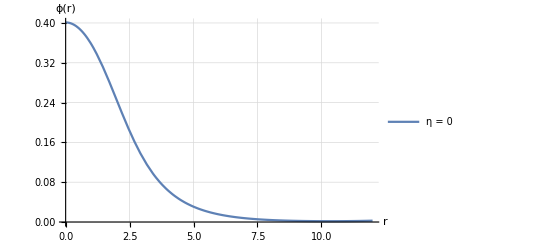

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,12},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
a=SeidelEqsList[[1]]/.(SeidelBCList[[1]]/.rMin-> r/.Equal-> Rule)//Simplify
```

{φ''[r]==(-1.59848×10^-8+0.000376697 r-1.2819 r^2+(-0.000113009+1.13009 r-0.000188349 r^2) gg'[r]+0.000113009 r NN''[r])/(3.64986×10^-9-0.0000483697 r+1. r^2),(1.71874×10^-8)/r+1. r==0.000271874,gg'[r]==-(1.85955×10^-9)/r+0.557866 r+0.0000843399 φ''[r]}

```mathematica
NSolve[a[[2]],r]
```

{{r→0.000171874},{r→0.0001}}

### data

```mathematica
Etam03={{0.001,1.00327793625,200,30, -0.3,10^-6},{0.005,1.016833476,50,30, -0.3,10^-8},{0.007,1.02388729657578,40,30,-0.3,10^-8},
{0.008,1.0274865425,40,30,-0.3,10^-6},{0.01,1.03483418567889,40.0,30,-0.3,10^-6},{0.012,1.04239623,30,30,-0.3,10^-8},
{0.015,1.054140552042320860,28,30,-0.3,10^-8},{0.02,1.074838765,28,30,-0.3,10^-8},{0.025,1.097106,28,30,-0.3,10^-8},
{0.028,1.1112783,28,30,-0.3,10^-8},{0.03,1.121086874,28,30,-0.3,10^-8},{0.04,1.1748856363351694,20,30,-0.3,10^-8},
{0.042,1.186707863351694,20,30,-0.3,10^-8},{0.044,1.198901393441151350,20,30,-0.3,10^-8},{0.046,1.211505343101943020,20,30,-0.3,10^-8},
{0.048,1.224518674759,20,30,-0.3,10^-8},{0.05,1.23797072572627,20,30,-0.3,10^-8},{0.052,1.25187767561304990,20,30,-0.3,10^-8},
{0.054,1.26625468873317999,20,30,-0.3,10^-8},{0.056,1.281110391763441167405,18,30,-0.3,10^-8},{0.058,1.29647849577,16,30,-0.3,10^-8},
{0.06,1.3124032435360,16,30,-0.3,10^-8},{0.07,1.4008143125450540,16,30,-0.3,10^-8},{0.08,1.5063484517423,12,30,-0.3,10^-8},{0.09,1.633272745017423,12,30,-0.3,10^-8}};
```

```mathematica
Eta03={{0.0001,1.0003256998,500,30,0.3,10^-6},{0.0003,1.000978223655,500,30,0.3,10^-5},{0.0005,1.0016317435,300,30,0.3,10^-6},{0.0007,1.00228644,200,30,0.3,10^-6},{0.0009,1.002942285,200,30,0.3,10^-6},{0.001,1.003270638,200,30,0.3,10^-6},{0.0013,1.00425742,200,30,0.3,10^-6},(*{0.0015,1.00491662,150,30,0.3,10^-6},*){0.0017,1.0055770939968,140,30,0.3,10^-6},
{0.0019,1.006238575,140,30,0.3,10^-6},{0.003,1.009897474,140,30,0.3,10^-5},{0.005,1.0166384235237,80,30,0.3,10^-5},
{0.006,1.02005146416,60,30,0.3,10^-5},{0.0065,1.0217684,60,30,0.3,10^-5},{0.0067,1.0224568,60,30,0.3,10^-5},
{0.00673,1.02256,60,30,0.3,10^-5},{0.00675,1.0226293,60,30,0.3,10^-5},{0.00678,1.0227326,60,30,0.3,10^-5},
{0.0068,1.02280181,60,30,0.3,10^-5},{0.0069,1.0231467,60,30,0.3,10^-5},{0.007,1.02349218,60,30,0.3,10^-5},
{0.0072,1.02418,40,30,0.3,0.4*10^-5},{0.0074,1.02487,40,30,0.3,0.4*10^-5},{0.0076,1.02556,40,30,0.3,10^-5},
 {0.0078,1.02626,40,30,0.3,0.4*10^-5},{0.008,1.02695,40,30,0.3,0.4*10^-5},{0.0086,1.02905,40,30,0.3,0.4*10^-5},{0.0088,1.029753,40,30,0.3,0.4*10^-5},{0.009,1.03045,40,30,0.3,0.4*10^-5},{0.0094,1.0318568,40,30,0.3,10^-5},
{0.01,1.0339767,40,30,0.3,0.4*10^-5},{0.010009,1.03401,30,30,0.3,0.4*10^-5},{0.0102,1.03467,30,30,0.3,0.4*10^-5},{0.0107,1.03644,30,30,0.3,0.4*10^-5},{0.0109,1.03721,25,30,0.3,10^-8},{0.011,1.03751,30,30,0.3,10^-8},
{0.0115,1.03932,30,30,0.3,10^-5},{0.012,1.041114,40,30,0.3,10^-5},{0.015,1.05201083,40,30,0.3,10^-6},
{0.018,1.0631343,32,30,0.3,10^-6},{0.019,1.06687854,26,30,0.3,10^-6},{0.02,1.070630178,23,30,0.3,10^-6},{0.022,1.0783017,21,30,0.3,10^-6},{0.025,1.089844,20,30,0.3,10^-6},{0.03,1.10946951,30,30,0.3,10^-8},{0.031,1.1134168,30,30,0.3,10^-8},{0.032,1.11736085,24,30,0.3,10^-8},{0.033,1.1213,20,30,0.3,10^-8},{0.034,1.12524,20,30,0.3,10^-8},{0.035,1.1291682,19,30,0.3,10^-8}};(*0.4*10^-5*)
```

### Checking

Mass

```mathematica
Dat=Etam03;
```

```mathematica
Table[
AA=Dat[[i]];
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=AA[[6]];
ϕ0=AA[[1]]*√(8π);
w=AA[[2]];
rMax=AA[[3]];
c4=1/2;
d4=1;
L3=(1/η)^(1/3);
N0=1;

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(*s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]; , *)

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; (*φ*)
(*Print[i];*)
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[Dat]}](*Length[Dat]*)
```

## N_95

d^3 x=r^2 Sin[θ]dr dθ dϕ=4π r^2 dr

Q=∫√-g j^0 ⅆ^3 x

```mathematica
j0H[r_]:=2 w (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 r gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]));
```

```mathematica
(*j0H[r_]:=2 w (ϕ[r]^2-(2 c (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]));*)
```

```mathematica
data=Etam03;
```

```mathematica
dataE={};
```

```mathematica
Clear[w, s0,s1,AA,rMax,rlim,c4];
```

```mathematica
Do[
AA=data[[i]];

Print[i];

SeidelBCList={};
Clear[rMin,ϕ0,r,c4,α,η,L1,w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];

(* Solving *)
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=AA[[6]];
ϕ0=AA[[1]]*√(8π);
w=AA[[2]];
rMax=AA[[3]];
c4=1/2;
d4=1;
L3=(1/η)^(1/3);
N0=1;
Print[rMin];

s0=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Print[s0];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s0]*Evaluate[gg[rMax]/.s0]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

(* Solving again *)
SeidelBCList={};
Clear[ w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];

N0= B[[1,1,1,2]];
w=w2(*w2*);
(*w=71036896476977879; Length[data]*)
(*w=0.738989172858; Length[data]-1*)
(*w=0.76869152435647894; Length[data]-2*)
(*w=0.799313552915709945; Length[data]-3*)
(*w=0.80545506106714612; Length[data]-4*)
(*w=0.81183343798750238; Length[data]-5*)
(*w=0.818182212202588424; Length[data]-6*)
(*w=0.82452812492940038; Length[data]-7*)
(*w=0.84381141855544345; Length[data]-10*)
(*w=0.85025826154451096; Length[data]-11*)
(*w=0.86339636666832317;; Length[data]-13*)
(*w=0.89691166882253148; Length[data]-14*)
(*w=0.9036454077891467; Length[data]-15*)
(*w=0.91379315867164682; Length[data]-16*)
(*w=0.94812141164018564; Length[data]-18*)
(*w=0.98265313357974503; 2*)
(*w=0.9757011495831277; 3*)
(*w=0.97222244543742713; 4*)
(*w=; 5*)
Print[w];

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Print[s1];
Clear[rlim, ϕ20,r0,enc];
ϕ20=ϕ0;
r0=rMin;
enc=0;
Do[
temp=ϕ20;
rtemp=r0;
If[Evaluate[φ[rB]/.s1][[1]]>temp||Evaluate[φ[rB]/.s1][[1]]<0,
(*Print[temp, "no cumplió ",Evaluate[φ[rB]/.s1][[1]]];*)
rlim=N[rtemp];
enc=1;
Break[],
ϕ20=Evaluate[φ[rB]/.s1][[1]];
r0=rB
],
{rB,rMin,rMax,0.001}];
If[enc==0,rlim=rMax];

Print[rlim, " ", rMax];

Print[
Plot[Evaluate[φ[r]/.s1],{r,rMin,rlim},PlotLegends->{Evaluate[φ[rMax]/.s1]}]
];
NE=NIntegrate[((Evaluate[gg[r]/NN[r]]/.s1)*Evaluate[j0H[r]/.s1])r^2 Sin[θ],{r,rMin,rlim},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"];N95=NE[[1]];(*0.95*)
(*Print[N95];*)
AppendTo[dataE,{ϕ0,N95}];
,{i,5,5}]
```

```mathematica
dataE
```

{{0.0401061,10.0729}}

```mathematica
w=0.9653393414152792;
NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

NDSolve::ndcf: Repeated convergence test failure at r == 26.0144; unable to continue.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

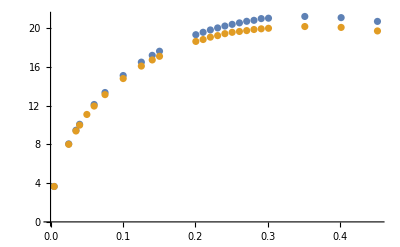

```mathematica
ListPlot[{{{0.005013256549262,3.6555208051491563},{0.025066282746310002,8.04923843522957},{0.035092795844834004,9.457688127183156},{0.040106052394096,10.072879332260994},{0.060159078591144007,12.114911689177822},{0.07519884823893,13.351774589711534},{0.10026513098524001,15.10426292976263},{0.12533141373155002,16.485628335517454},{0.14037118337933602,17.186497965845422},{0.15039769647786,17.61155067255943},{0.20053026197048002,19.316627519785012},{0.21055677506900403,19.567092470005537},{0.220583288167528,19.807494741632794},{0.23060980126605202,20.016779652276767},{0.24063631436457603,20.21254863841478},{0.25066282746310004,20.38507814849907},{0.260689340561624,20.53869571842294},{0.270715853660148,20.70039094123267},{0.28074236675867204,20.800246063619028},{0.290768879857196,20.977690305252015},{0.30079539295572,21.019646686094497},{0.35092795844834007,21.199092130825463},{0.40106052394096003,21.07811587134297},{0.45119308943358005,20.68933090343293}},MvsrhoEtam03}]
```

```mathematica
NvsrhoEta0={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6344689243669515},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.093294025651763},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.389143311712792},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.738511485711928},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.076240041515835},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.391507895830112},{0.024063631436457602715132155045322590836670091247431265286`30.,7.691061021525971},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.9749699499700295},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.15611678513496},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.604579160671012},{0.0521378681123248080569397927063501881413711934354659082782`30.,10.749547997536158},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.688882097927479},{0.076869933755350677876517861520956946722713119839664403182`30.,12.474349996099205},{0.0892359665768636171346138094778961420038894078404933176173`30.,13.138956273790598},{0.1016019993983765650893235845341069692660763454387815660195`30.,13.705803165017066},{0.1139680322198894782575780511932312686042206846472324785541`30.,14.190997254523827},{0.1263340650414024262122878262494420958664076222455207269563`30.,14.606872958287264},{0.1387000978629153567737699471071096591665732606488903074248`30.,14.96334212510879},{0.1510661306844282873352520679647772224667388990522598878932`30.,15.267346230213944},{0.1634321635059412526831894972195313136909471358454668042291`30.,15.524853057614093},{0.1757981963274541832446716180771988769911127742488363846976`30.,15.7415387574424},{0.188164229148967113806153738934866440291278412652205965166`30.,15.921433794992211},{0.2005302619704800443676358597925340035914440510555755456344`30.,16.0691069854778},{0.2105567750690040552826314798814323357520269032058136568832`30.,16.166172523521126},{0.2205832881675280314111717915732441399885671569662144322642`30.,16.245057512177937},{0.2306098012660520423261674116621424721491500091164525435128`30.,16.307558876622075},{0.2406363143645760532411630317510408043097328612666906547614`30.,16.354148176203985},{0.2506628274631000641561586518399391364703157134169287660099`30.,16.386371012830114},{0.2606893405616240402846989635317509407068559671773295413911`30.,16.405402427769854},{0.2707158536601480511996945836206492728674388193275676526397`30.,16.411620497365075},{0.2807423667586720621146902037095476050280216714778057638883`30.,16.406334088029773},{0.2907688798571960730296858237984459371886045236280438751368`30.,16.390071647944378},{0.300795392955720049158226135490257741425144777388444650518`30.,16.36359386836756},{0.3509279584483401037332042359347494022280590381396352067611`30.,16.099649623751525},{0.40106052394096008873527171958506800718`14.,15.660987806796697},{0.451193089433580073737339203235386612137717166082666975777`30.,15.095324704743305},{0.50132565492620012831231730367987827294063142683385753202`30.,14.438988649163349},{0.551458220418820113314384787330196877895460490805373416528`30.,13.719937361701037},{0.651723351404060152891430371425007143653203815528079857279`30.,12.182956507770463},{0.751988482389300122895565338725644353562861943471111626295`30.,10.637500487422159},{0.7620149954878241338105609588145426857234447956213497375436`30.,10.495296258856612},{0.7981104426425106009337094378522459038407771420740768067326`30.,9.97002420254333},{0.8021210478819201774705434391701360143657762042223021825381`30.,9.904329626336184},{0.8342058897971969289110366833016030102619390949674545324515`30.,9.469426475291582},{0.8522536133745402320455215396146276751686904649734927387811`30.,9.219914535133883},{0.8703013369518833960341851623393062283792714414201816016404`30.,8.999903777649925},{0.9063967841065697240115124077886633348004333943135593273595`30.,8.568016765185737},{0.9424922312612561911346608868263665529177657407662863965484`30.,8.180216364800447},{0.952518744359780202049656506915264885078348592916524507797`30.,8.067685505407704},{1.00265130985240025662463460735975654588126285366771506404`30.,7.6347647044728015},{1.1029164408376402266287695746603937557909209816107468330559`30.,7.128355030106395},{1.2533141373155002512078826424055226265034933703049691583149`30.,7.263694171435854},{1.5039769647786002457911306774512887071257238869422232525899`30.,8.190294741941976}};
```

```mathematica
NvsrhoBEtam03={{0.005013256549262,3.6555208051491563},{0.025066282746310002,8.04923843522957},{0.035092795844834004,9.457688127183156},{0.040106052394096,10.072879332260994},{0.060159078591144007,12.114911689177822},{0.07519884823893,13.351774589711534},{0.10026513098524001,15.10426292976263},{0.12533141373155002,16.485628335517454},{0.14037118337933602,17.186497965845422},{0.15039769647786,17.61155067255943},{0.20053026197048002,19.316627519785012},{0.21055677506900403,19.567092470005537},{0.220583288167528,19.807494741632794},{0.23060980126605202,20.016779652276767},{0.24063631436457603,20.21254863841478},{0.25066282746310004,20.38507814849907},{0.260689340561624,20.53869571842294},{0.270715853660148,20.70039094123267},{0.28074236675867204,20.800246063619028},{0.290768879857196,20.977690305252015},{0.30079539295572,21.019646686094497},{0.35092795844834007,21.199092130825463},{0.40106052394096003,21.07811587134297},{0.45119308943358005,20.68933090343293}};
```

```mathematica
NvsrhoBEta03={{0.0005013256549262,1.1595440267942034},{0.0015039769647786,2.001216673938398},{0.002506628274631,2.5757808419117176},{0.0035092795844834,3.0389728970255048},{0.004511930894335801,3.435379736891762},{0.005013256549262,3.616486255832679},{0.0065172335140406,4.10456539874522},{0.0085225361337454,4.6660881080750105},{0.0095251874435978,4.918429261097283},{0.015039769647786002,6.081097760340285},{0.025066282746310002,7.618709858654019},{0.030079539295572003,8.222000721139333},{0.032586167570203,8.495148004950481},{0.0335888188800554,8.601392943940947},{0.03373921657653326,8.618079960696244},{0.0338394817075185,8.626420206705763},{0.03398987940399636,8.64250504180393},{0.0340901445349816,8.65139744195267},{0.034591470189907804,8.702857196834495},{0.035092795844834004,8.752228524091729},{0.036095447154686405,8.867431511371379},{0.037098098464538806,8.97387435678074},{0.0381007497743912,9.08175166675653},{0.043114006323653205,9.496572096804039},{0.044116657633505606,9.567656096945221},{0.045119308943358,9.663533987069943},{0.04712461156306281,9.814792043746632},{0.050132565492620004,10.024246720771666},{0.050177684801563364,10.016840849547648},{0.051135216802472405,10.14109149488166},{0.0536418450771034,10.321104728960234},{0.057652450316513004,10.48737409917517},{0.060159078591144007,10.630182075902516},{0.07519884823893,11.352861495151284},{0.090238617886716,11.878962287052413},{0.095251874435978,12.043359743532763},{0.10026513098524001,12.220393110389947},{0.110291644083764,12.288641775778125},{0.12533141373155002,12.587835773289862},{0.15039769647786,12.656687414428191},{0.15541095302712202,12.663460722163947},{0.160424209576384,12.652779458958184},{0.16543746612564603,12.651518760169122},{0.17045072267490802,12.631047689371552},{0.17546397922417004,12.565980025371989}};
```

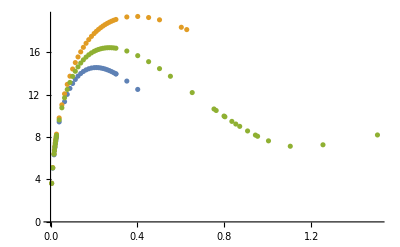

```mathematica
ListPlot[{NvsrhoBEta03,NvsrhoBEtam03,NvsrhoEta0},AxesOrigin->{0,0},PlotLegends->Automatic;FrameLabel->{"ρ0","N|M"},PlotRange->All]
```

```mathematica
PlotTheme->"Scientific"
```

```mathematica
Export["N_BS.dat",NvsrhoEta0]
```

N_BS.dat

## Masa

```mathematica
SeidelBCList={};
Clear[rMin,ϕ0,r,c4,α,η,L1,w,N0,mS,k];

AppendTo[SeidelBCList,{NN[rMin]==N0,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

{{53.6443,3.65435},{23.6263,8.00215},{19.8869,9.38078},{18.5827,9.98401},{16.7183,11.0866},{14.9199,11.9537},{13.1795,13.1336},{11.3094,14.7914},{9.96573,16.0788},{9.30624,16.7128},{8.91405,17.0879},{7.5255,18.6241},{7.25663,18.8199},{7.0971,19.0647},{6.85992,19.2223},{6.71661,19.424},{6.52621,19.5641},{6.30113,19.6504},{6.11162,19.7405},{5.97078,19.8525},{5.80742,19.9233},{5.65378,19.9795},{5.04758,20.1604},{4.52961,20.069},{4.04523,19.7044}}

{{0.00501326,3.65435},{0.0250663,8.00215},{0.0350928,9.38078},{0.0401061,9.98401},{0.0501326,11.0866},{0.0601591,11.9537},{0.0751988,13.1336},{0.100265,14.7914},{0.125331,16.0788},{0.140371,16.7128},{0.150398,17.0879},{0.20053,18.6241},{0.210557,18.8199},{0.220583,19.0647},{0.23061,19.2223},{0.240636,19.424},{0.250663,19.5641},{0.260689,19.6504},{0.270716,19.7405},{0.280742,19.8525},{0.290769,19.9233},{0.300795,19.9795},{0.350928,20.1604},{0.401061,20.069},{0.451193,19.7044}}

{{0.996529,3.47163},{0.982653,7.60204},{0.975701,8.91174},{0.972222,9.48481},{0.965239,10.5323},{0.958417,11.356},{0.948121,12.4769},{0.930848,14.0519},{0.913794,15.2749},{0.903645,15.8772},{0.896912,16.2335},{0.863397,17.6929},{0.856896,17.8789},{0.850259,18.1114},{0.843811,18.2612},{0.83726,18.4528},{0.830839,18.5859},{0.824528,18.6678},{0.818212,18.7534},{0.811833,18.8599},{0.805551,18.9271},{0.799355,18.9805},{0.768693,19.1524},{0.73899,19.0655},{0.71069,18.7192}}

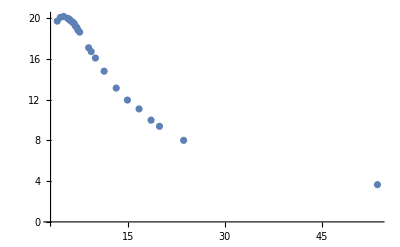

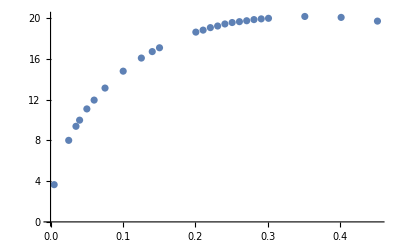

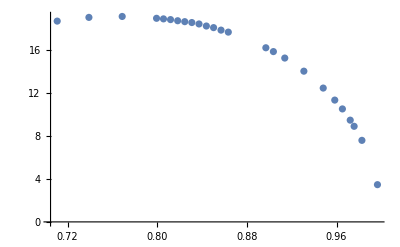

```mathematica
mvsr={};
phivswf={};
wfvsm={};
stop2=0;

For[j=1,j<Length[Etam03]+1,j++,
Print[j];

AA=Etam03[[j]];
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=AA[[6]];
ϕ0=AA[[1]]*√(8π);
w=AA[[2]];
rMax=AA[[3]];
c4=1/2;
d4=1;
L3=(1/η)^(1/3);
N0=1;

Clear[s,M95, M];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]8π; 

M95=0.95M[rMax][[1]];

(* comprobando ϕ pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<4*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Break[]];

(* calculando radio *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];

Print[rad];
Print["masa95 = ", M95];

(* calculando frecuencia*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

AppendTo[mvsr,{rad[[2]],M[rMax][[1]]}];
AppendTo[phivswf,{ϕ0,M[rMax][[1]]}];
AppendTo[wfvsm,{w2,M95}];
](* FOR *)
(* Resultados *)

mvsr
phivswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full]}]
Show[{ListPlot[phivswf,PlotRange->Full]}]
Show[{ListPlot[wfvsm,PlotRange->Full]}]
```

```mathematica
MvsrhoEta0={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6328627006313905},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.082070127778417},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.366909747109032},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.711464105023235},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.044978836694404},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.355499301452053},{0.024063631436457602715132155045322590836670091247431265286`30.,7.650400274177276},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.9294471357651375},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.107334581306757},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.523540178234157},{0.0521378681123248080569397927063501881413711934354659082782`30.,10.673210177382693},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.897979780775408},{0.076869933755350677876517861520956946722713119839664403182`30.,12.357746132480019},{0.0892359665768636171346138094778961420038894078404933176173`30.,12.942240299452099},{0.1016019993983765650893235845341069692660763454387815660195`30.,13.448731516270238},{0.1139680322198894782575780511932312686042206846472324785541`30.,13.936642806525098},{0.1263340650414024262122878262494420958664076222455207269563`30.,14.516060023810821},{0.1387000978629153567737699471071096591665732606488903074248`30.,14.697887942766961},{0.1510661306844282873352520679647772224667388990522598878932`30.,14.928837709759483},{0.1634321635059412526831894972195313136909471358454668042291`30.,15.195899032404938},{0.1757981963274541832446716180771988769911127742488363846976`30.,15.340432311303124},{0.2005302619704800443676358597925340035914440510555755456344`30.,15.609676986397568},{0.2105567750690040552826314798814323357520269032058136568832`30.,15.695351690497573},{0.2205832881675280314111717915732441399885671569662144322642`30.,15.764664732424825},{0.2306098012660520423261674116621424721491500091164525435128`30.,15.857562696139526},{0.2406363143645760532411630317510408043097328612666906547614`30.,15.859403393657516},{0.2506628274631000641561586518399391364703157134169287660099`30.,15.88724966856022},{0.2606893405616240402846989635317509407068559671773295413911`30.,15.903562231251215},{0.2707158536601480511996945836206492728674388193275676526397`30.,15.908929743835072},{0.2807423667586720621146902037095476050280216714778057638883`30.,15.904401941579051},{0.2907688798571960730296858237984459371886045236280438751368`30.,15.890659488439866},{0.300795392955720049158226135490257741425144777388444650518`30.,15.868326636234166},{0.3509279584483401037332042359347494022280590381396352067611`30.,15.837848924583763},{0.40106052394096008873527171958506800718`14.,15.29471342277625},{0.451193089433580073737339203235386612137717166082666975777`30.,14.83766598303419},{0.50132565492620012831231730367987827294063142683385753202`30.,14.319171373414953},{0.551458220418820113314384787330196877895460490805373416528`30.,13.758073328161377},{0.651723351404060152891430371425007143653203815528079857279`30.,12.571642879185461},{0.751988482389300122895565338725644353562861943471111626295`30.,11.384623131343705},{0.7620149954878241338105609588145426857234447956213497375436`30.,11.275141431617783},{0.7981104426425106009337094378522459038407771420740768067326`30.,10.86972374904789},{0.8021210478819201774705434391701360143657762042223021825381`30.,10.818832407324988},{0.8342058897971969289110366833016030102619390949674545324515`30.,10.481245539903998},{0.8522536133745402320455215396146276751686904649734927387811`30.,10.286707917768963},{0.8703013369518833960341851623393062283792714414201816016404`30.,10.114913801052868},{0.9063967841065697240115124077886633348004333943135593273595`30.,9.774502245962568},{0.9424922312612561911346608868263665529177657407662863965484`30.,9.466227702494441},{0.952518744359780202049656506915264885078348592916524507797`30.,9.376184614301476},{1.00265130985240025662463460735975654588126285366771506404`30.,9.026900146656342},{1.1029164408376402266287695746603937557909209816107468330559`30.,8.61027335055167},{1.2533141373155002512078826424055226265034933703049691583149`30.,8.726448249258695},{1.5039769647786002457911306774512887071257238869422232525899`30.,9.517769597308938}};
```

```mathematica
MvsrhoEtam03={{0.005013256549262,3.654349018446014},{0.025066282746310002,8.002147049508832},{0.035092795844834004,9.380781491881727},{0.040106052394096,9.984014611131718},{0.050132565492620004,11.086613923357195},{0.060159078591144007,11.953653698916076},{0.07519884823893,13.13360664306886},{0.10026513098524001,14.791438398963804},{0.12533141373155002,16.078821089340018},{0.14037118337933602,16.71284247289949},{0.15039769647786,17.087925385213765},{0.20053026197048002,18.624125501837128},{0.21055677506900403,18.81985102792953},{0.220583288167528,19.064680996018957},{0.23060980126605202,19.222265597676373},{0.24063631436457603,19.42402008615071},{0.25066282746310004,19.5641452979092},{0.260689340561624,19.650355363162994},{0.270715853660148,19.740453325605444},{0.28074236675867204,19.852496644839267},{0.290768879857196,19.923278059648307},{0.30079539295572,19.979512409087786},{0.35092795844834007,20.160445185445887},{0.40106052394096003,20.068973663353923},{0.45119308943358005,19.704400514750244}};
```

```mathematica
MvsrhoEta03={{0.0005013256549262,1.1623688930457154},{0.0015039769647786,2.0014431455073836},{0.002506628274631,2.5742595738477414},{0.0035092795844834,3.037755511794873},{0.004511930894335801,3.4327063838925853},{0.005013256549262,3.6138701933920903},{0.0065172335140406,4.101064064432191},{0.0085225361337454,4.658097638944882},{0.0095251874435978,4.908842255952731},{0.015039769647786002,6.0620369271710475},{0.025066282746310002,7.651481172617003},{0.030079539295572003,8.17150508742887},{0.032586167570203,8.438555015795728},{0.0335888188800554,8.548730486376112},{0.03373921657653326,8.574961915589821},{0.0338394817075185,8.569208358506074},{0.03398987940399636,8.590443997294507},{0.0340901445349816,8.592482196602784},{0.034591470189907804,8.651660185746174},{0.035092795844834004,8.697141905569959},{0.036095447154686405,8.802657409634907},{0.037098098464538806,8.911280359129423},{0.0381007497743912,9.027618697348114},{0.0391034010842436,9.084716617207224},{0.040106052394096,9.214781364030797},{0.043114006323653205,9.428105977829771},{0.044116657633505606,9.49043486636181},{0.045119308943358,9.606353945128102},{0.04712461156306281,9.759254741390409},{0.050132565492620004,9.959653226642928},{0.050177684801563364,9.919760109503292},{0.051135216802472405,10.04065044770064},{0.0536418450771034,10.224100017818127},{0.05464449638695581,10.107346614087314},{0.055145822041882,10.31187232691571},{0.057652450316513004,10.374481209927259},{0.060159078591144007,10.515924143324828},{0.07519884823893,11.230362734918618},{0.090238617886716,11.715270521158564},{0.095251874435978,11.872733733193341},{0.10026513098524001,12.046263871417786},{0.110291644083764,12.11743982221464},{0.12533141373155002,12.373754888731863},{0.15039769647786,12.509816208839696},{0.15541095302712202,12.471465316061966},{0.160424209576384,12.445458656431375},{0.16543746612564603,12.4371553150165},{0.17045072267490802,12.432013841492358},{0.17546397922417004,12.421842654870225}};
```

```mathematica
RvsMEtam03={{53.644330399421165,3.654349018446014},{23.626303138551105,8.002147049508832},{19.886859238308787,9.380781491881727},{18.582725160689126,9.984014611131718},{16.71826715565055,11.086613923357195},{14.919869075877386,11.953653698916076},{13.179469843381275,13.13360664306886},{11.309359274412515,14.791438398963804},{9.965725254548591,16.078821089340018},{9.306236275572527,16.71284247289949},{8.91405387694145,17.087925385213765},{7.525501276775288,18.624125501837128},{7.25662872020362,18.81985102792953},{7.097103618838195,19.064680996018957},{6.859923664470544,19.222265597676373},{6.716608463310348,19.42402008615071},{6.5262056885691395,19.5641452979092},{6.301132811576793,19.650355363162994},{6.111621263310665,19.740453325605444},{5.9707790486975565,19.852496644839267},{5.807422501837726,19.923278059648307},{5.653783165236952,19.979512409087786},{5.047580079292602,20.160445185445887},{4.529612412291383,20.068973663353923},{4.045227661845819,19.704400514750244}};
```

```mathematica
RvsMEta03={{171.33476399700086,1.1623688930457154},{97.98684577347768,2.0014431455073836},{75.72111473520505,2.5742595738477414},{64.03159326897344,3.037755511794873},{56.373636795737596,3.4327063838925853},{53.504003382630984,3.6138701933920903},{46.87527031896273,4.101064064432191},{40.853149371993,4.658097638944882},{38.60442555618825,4.908842255952731},{30.571864599700387,6.0620369271710475},{24.271101857199053,7.651481172617003},{21.28990562374234,8.17150508742887},{20.410051902512443,8.438555015795728},{20.148415765107448,8.548730486376112},{20.190340621425623,8.574961915589821},{20.033354989687396,8.569208358506074},{20.035303441986642,8.590443997294507},{19.942898427815187,8.592482196602784},{19.865530755144427,8.651660185746174},{19.690111244178993,8.697141905569959},{19.431720914329926,8.802657409634907},{19.23839036396229,8.911280359129423},{19.119465915138584,9.027618697348114},{18.673904370995203,9.084716617207224},{18.681400855390216,9.214781364030797},{17.778160395801578,9.428105977829771},{17.472786611340144,9.49043486636181},{17.480831533671886,9.606353945128102},{17.104833613835808,9.759254741390409},{16.490253833736702,9.959653226642928},{16.236893602644816,9.919760109503292},{16.28949059611567,10.04065044770064},{15.965577714067564,10.224100017818127},{15.189610980758385,10.107346614087314},{15.710473670744584,10.31187232691571},{15.021010660192466,10.374481209927259},{14.68859716959436,10.515924143324828},{13.058787096202842,11.230362734918618},{11.728027039968163,11.715270521158564},{11.437342352478902,11.872733733193341},{11.24733047325408,12.046263871417786},{10.374443991374234,12.11743982221464},{9.764052444266698,12.373754888731863},{8.882397278491059,12.509816208839696},{8.613764269486056,12.471465316061966},{8.404599398181393,12.445458656431375},{8.262993289623925,12.4371553150165},{8.1585153523298,12.432013841492358},{8.058550114685207,12.421842654870225}};
```

```mathematica
RvsMEta0={{53.54420398875108,3.6328627006313905},{37.64106430595025,5.082070127778417},{29.814058404008005,6.366909747109032},{27.927353490970727,6.711464105023235},{26.451164919920632,7.044978836694404},{25.155185568214495,7.355499301452053},{24.042498156118924,7.650400274177276},{23.05711848924741,7.9294471357651375},{22.460020873741467,8.107334581306757},{18.467178440734923,9.523540178234157},{16.185508560256295,10.673210177382693},{13.18662478539851,12.357746132480019},{11.960222305330236,12.942240299452099},{11.027255498562669,13.448731516270238},{10.412228338990149,13.936642806525098},{8.808210528375358,14.928837709759483},{8.465594448127314,15.195899032404938},{7.991872434382174,15.340432311303124},{7.317614895270514,15.609676986397568},{7.093239544185862,15.695351690497573},{6.884014004316706,15.764664732424825},{6.749637961822022,15.857562696139526},{6.504156037664138,15.859403393657516},{6.331314249309371,15.88724966856022},{6.1685353631781705,15.903562231251215},{6.014608647845447,15.908929743835072},{5.869012484747898,15.904401941579051},{5.730972782777869,15.890659488439866},{5.5997980817850355,15.868326636234166},{5.300313368686874,15.837848924583763},{4.5796400102994355,15.29471342277625},{4.201184164336634,14.83766598303419},{3.8900345130162575,14.319171373414953},{3.629309473783122,13.758073328161377},{3.225744354246993,12.571642879185461},{2.953650105328868,11.384623131343705},{2.9342124305338078,11.275141431617783},{2.8705160405855743,10.86972374904789},{2.8634231244642008,10.818832407324988},{2.8228505205446055,10.481245539903998},{2.804633277676073,10.286707917768963},{2.7928112802479252,10.114913801052868},{2.7795289683735938,9.774502245962568},{2.785502264493303,9.466227702494441},{2.79144566929839,9.376184614301476},{2.8425346098841655,9.026900146656342},{3.058574219170653,8.61027335055167},{3.490500042230311,8.726448249258695},{3.6418317329905445,9.517769597308938}};
```

```mathematica
ListPlot[{MvsrhoEta03,NvsrhoEta03,MvsrhoEta0,NvsrhoEta0,MvsrhoEtam03,NvsrhoEtam03},Joined->False,PlotTheme->"Scientific"]
```

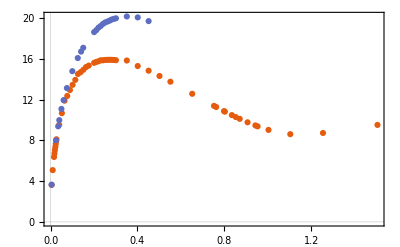

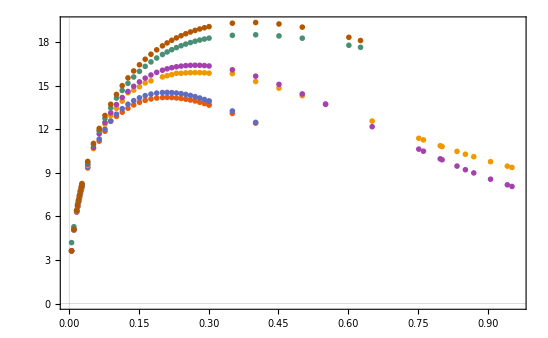

```mathematica
ListPlot[{MvsrhoEta0,MvsrhoEtam03},Joined->False,PlotTheme->"Scientific"]
```

```mathematica
Export["NvsrhoBEtam03.dat",NvsrhoBEtam03]
Export["NvsrhoBEta03.dat",NvsrhoBEta03]
Export["NvsrhoEta0.dat",NvsrhoEta0]
```

NvsrhoBEtam03.dat

NvsrhoBEta03.dat

NvsrhoEta0.dat

## Interpolations

```mathematica
(*masa vs radio*)
```

```mathematica
RvsMEtam03={{53.644330399421165,3.654349018446014},{23.626303138551105,8.002147049508832},{19.886859238308787,9.380781491881727},{18.582725160689126,9.984014611131718},{16.71826715565055,11.086613923357195},{14.919869075877386,11.953653698916076},{13.179469843381275,13.13360664306886},{11.309359274412515,14.791438398963804},{9.965725254548591,16.078821089340018},{9.306236275572527,16.71284247289949},{8.91405387694145,17.087925385213765},{7.525501276775288,18.624125501837128},{7.25662872020362,18.81985102792953},{7.097103618838195,19.064680996018957},{6.859923664470544,19.222265597676373},{6.716608463310348,19.42402008615071},{6.5262056885691395,19.5641452979092},{6.301132811576793,19.650355363162994},{6.111621263310665,19.740453325605444},{5.9707790486975565,19.852496644839267},{5.807422501837726,19.923278059648307},{5.653783165236952,19.979512409087786},{5.047580079292602,20.160445185445887},{4.529612412291383,20.068973663353923},{4.045227661845819,19.704400514750244}};

RvsMEta03={{171.33476399700086,1.1623688930457154},{97.98684577347768,2.0014431455073836},{75.72111473520505,2.5742595738477414},{64.03159326897344,3.037755511794873},{56.373636795737596,3.4327063838925853},{53.504003382630984,3.6138701933920903},{46.87527031896273,4.101064064432191},{40.853149371993,4.658097638944882},{38.60442555618825,4.908842255952731},{30.571864599700387,6.0620369271710475},{24.271101857199053,7.651481172617003},{21.28990562374234,8.17150508742887},{20.410051902512443,8.438555015795728},{20.148415765107448,8.548730486376112},{20.190340621425623,8.574961915589821},{20.033354989687396,8.569208358506074},{20.035303441986642,8.590443997294507},{19.942898427815187,8.592482196602784},{19.865530755144427,8.651660185746174},{19.690111244178993,8.697141905569959},{19.431720914329926,8.802657409634907},{19.23839036396229,8.911280359129423},{19.119465915138584,9.027618697348114},{18.673904370995203,9.084716617207224},{18.681400855390216,9.214781364030797},{17.778160395801578,9.428105977829771},{17.472786611340144,9.49043486636181},{17.480831533671886,9.606353945128102},{17.104833613835808,9.759254741390409},{16.490253833736702,9.959653226642928},{16.236893602644816,9.919760109503292},{16.28949059611567,10.04065044770064},{15.965577714067564,10.224100017818127},{15.189610980758385,10.107346614087314},{15.710473670744584,10.31187232691571},{15.021010660192466,10.374481209927259},{14.68859716959436,10.515924143324828},{13.058787096202842,11.230362734918618},{11.728027039968163,11.715270521158564},{11.437342352478902,11.872733733193341},{11.24733047325408,12.046263871417786},{10.374443991374234,12.11743982221464},{9.764052444266698,12.373754888731863},{8.882397278491059,12.509816208839696},{8.613764269486056,12.471465316061966},{8.404599398181393,12.445458656431375},{8.262993289623925,12.4371553150165},{8.1585153523298,12.432013841492358},{8.058550114685207,12.421842654870225}};

RvsMEta0={{53.54420398875108,3.6328627006313905},{37.64106430595025,5.082070127778417},{29.814058404008005,6.366909747109032},{27.927353490970727,6.711464105023235},{26.451164919920632,7.044978836694404},{25.155185568214495,7.355499301452053},{24.042498156118924,7.650400274177276},{23.05711848924741,7.9294471357651375},{22.460020873741467,8.107334581306757},{18.467178440734923,9.523540178234157},{16.185508560256295,10.673210177382693},{13.18662478539851,12.357746132480019},{11.960222305330236,12.942240299452099},{11.027255498562669,13.448731516270238},{10.412228338990149,13.936642806525098},{8.808210528375358,14.928837709759483},{8.465594448127314,15.195899032404938},{7.991872434382174,15.340432311303124},{7.317614895270514,15.609676986397568},{7.093239544185862,15.695351690497573},{6.884014004316706,15.764664732424825},{6.749637961822022,15.857562696139526},{6.504156037664138,15.859403393657516},{6.331314249309371,15.88724966856022},{6.1685353631781705,15.903562231251215},{6.014608647845447,15.908929743835072},{5.869012484747898,15.904401941579051},{5.730972782777869,15.890659488439866},{5.5997980817850355,15.868326636234166},{5.300313368686874,15.837848924583763},{4.5796400102994355,15.29471342277625},{4.201184164336634,14.83766598303419},{3.8900345130162575,14.319171373414953},{3.629309473783122,13.758073328161377},{3.225744354246993,12.571642879185461},{2.953650105328868,11.384623131343705},{2.9342124305338078,11.275141431617783},{2.8705160405855743,10.86972374904789},{2.8634231244642008,10.818832407324988},{2.8228505205446055,10.481245539903998},{2.804633277676073,10.286707917768963},{2.7928112802479252,10.114913801052868},{2.7795289683735938,9.774502245962568},{2.785502264493303,9.466227702494441},{2.79144566929839,9.376184614301476},{2.8425346098841655,9.026900146656342},{3.058574219170653,8.61027335055167},{3.490500042230311,8.726448249258695},{3.6418317329905445,9.517769597308938}};
```

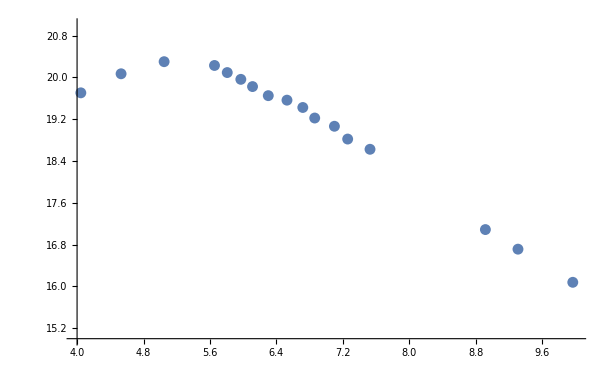

```mathematica
fig0=ListPlot[RvsMEtam03,PlotRange->{{4,10},{15,21}}]
```

```mathematica
RvsMEtam03={{53.644330399421165,3.654349018446014},{23.626303138551105,8.002147049508832},{19.886859238308787,9.380781491881727},{18.582725160689126,9.984014611131718},{16.71826715565055,10.776613923357195},{14.919869075877386,11.953653698916076},{13.179469843381275,13.13360664306886},{11.309359274412515,14.791438398963804},{9.965725254548591,16.078821089340018},{9.306236275572527,16.71284247289949},{8.91405387694145,17.087925385213765},{7.525501276775288,18.624125501837128},{7.25662872020362,18.81985102792953},{7.097103618838195,19.064680996018957},{6.859923664470544,19.222265597676373},{6.716608463310348,19.42402008615071},{6.5262056885691395,19.5641452979092},{6.301132811576793,19.650355363162994},{6.111621263310665,19.8240453325605444},{5.9707790486975565,19.962496644839267},{5.807422501837726,20.0923278059648307},{5.653783165236952,20.2279512409087786},{5.047580079292602,20.300445185445887},{4.529612412291383,20.068973663353923},{4.045227661845819,19.704400514750244}};
```

```mathematica
int=Interpolation[RvsMEtam03,InterpolationOrder->2,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
f=Interpolation[{#1,Log[#2]}&@@@RvsMEtam03,InterpolationOrder->2,Method->"Spline"]
```

InterpolatingFunction[…]

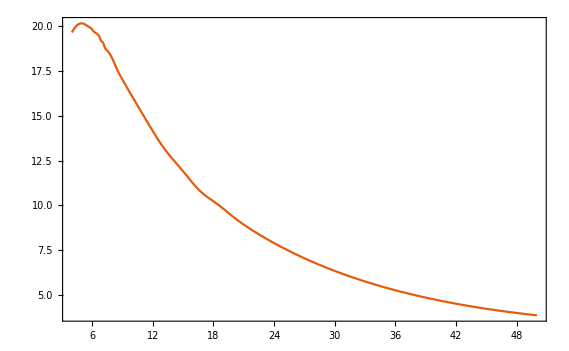

```mathematica
fig1=Plot[Exp@f[r],{r,4,50},PlotTheme->"Scientific"]
```

```mathematica
dat={};
Do[
AppendTo[dat,{r,Exp@f[r]}],{r,4,50,0.5}
]
```

```mathematica
dat
```

{{4,19.6567},{5,20.1634},{6,19.8317},{7,19.1397},{8,18.1983},{9,17.0018},{10,16.0457},{11,15.084},{12,14.1497},{13,13.2771},{14,12.5257},{15,11.9101},{16,11.4412},{17,10.9293},{18,10.3122},{19,9.77484},{20,9.33284},{21,8.92823},{22,8.5558},{23,8.20855},{24,7.88287},{25,7.57731},{26,7.29051},{27,7.02123},{28,6.76832},{29,6.53072},{30,6.30745},{31,6.0976},{32,5.90033},{33,5.71487},{34,5.54049},{35,5.37654},{36,5.2224},{37,5.0775},{38,4.94131},{39,4.81334},{40,4.69314},{41,4.58029},{42,4.4744},{43,4.37511},{44,4.28208},{45,4.19502},{46,4.11363},{47,4.03766},{48,3.96685},{49,3.90099},{50,3.83986}}

```mathematica
fig2=ListPlot[dat,PlotStyle->Gray,Joined->True];
```

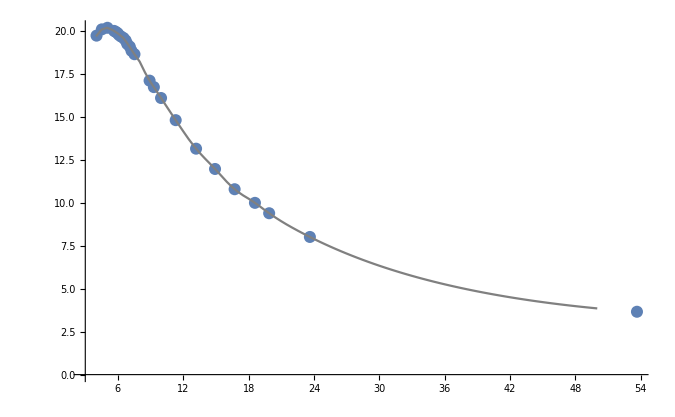

```mathematica
Show[{fig0,fig2}]
```